# TravelScope Exploration

## Load Data

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/DayJetDesktop/Travelscope/Travelscope2000/MSA_Travelscope"]
```

/Users/brucesawhill/Desktop/DayJetDesktop/Travelscope/Travelscope2000/MSA_Travelscope

```mathematica
msapops=<<msapops03;
usamsa=<<usamsa04;
usa04=<<usa04;
```

```mathematica
msapops=<<msapops48;
```

```mathematica
msapairdistancetable=<<msadistancetable;
```

```mathematica
msapairdistancetable=<<msadistancetable;
```

```mathematica
statsigprojector=<<statsigprojector;
```

```mathematica
leisurepairtrips=<<msaleisurepairtrips2000;
```

```mathematica
renormpairsmsa=<<renormpairsmsa;
```

```mathematica
msaleisuredata=<<msaleisuredata;
```

```mathematica
rmsaleisuredata=<<rmsaleisuredata;
```

```mathematica
FileNames[]
```

{.DS_Store,MSA_Population.txt,MSA_TS_Data2000.txt}

```mathematica
usamsa=Import["MSA_TS_Data2000.txt","CSV"];
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/MathematicaData"]
```

/Users/brucesawhill/Desktop/MathematicaData

```mathematica
usa06=<<travelscope06mma;
```

```mathematica
Length[usa06]
```

354207

```mathematica
Dimensions[usa06]
```

{354207}

```mathematica
usa06[[1]]
```

{71141,21133,12,FL378601,2,2,2,2,4,1551152,31530,313289714,1942340,51,21.3346,2,1.22005×10^8,GA,56.3281,19.81929304254.950259,18.3168,73.267,0,0,10,20051}

```mathematica
usamsa>>usamsa04;
```

```mathematica
FileNames[]
```

{150hubpop,2way,3parameterloglinearfit,3parameterloglinearinversewtfit,3parameterloglinearnowtfit,75hubpop,airports,allgrid,arr1,asymodpairsbizplus,asymodpairsbizplusfilter,asympairlist,asypairspeopledistbizplus,ats95allincomes,attrmatrix,auto,bizplotpairs,bizspendintensityptsusa04,bizspendintensityusa04,bizstars,bkstail,bts95mma,calibration750,characteristictimes,closebizports,corrmatrix,countmatrix,cumubizspendint,cumuleisspendint,drawusamma,.DS_Store,firmpops,flyratio,fmatrix,fpos,gravdata,hoursvisits,hyperpts,incomespendpts,intripmatrix,leisureplotpairs,leisureprecise,leisurewealthtrips,measurebar,modeproportions,msadistancetable,msahosp04,msaincomesmod03,msaintrips2000,msaleisuredata,msaleisuredatafilt,msaleisureintrips2000,msaleisureouttrips2000,msaleisurepairtrips2000,msaoccs04,msaoccsmod03,msaocctots04,msaonly,msaouttrips2000,msapops03,msapops0409,msapops48,msapopsmod03,mxvisit,newlistformat,noerrorfilteredflights,nonlinearfitinversewt,nonlinearfitlinearwt,nonlinearfitnowt,nonstops,nozeros,nozeros4k,odpairsbizplus,othertravel,outtripmatrix,pairspeopledistbizonly,pairspeopledistbizplus,phyloset,physicaljetairports,planeintrosched,planelist,popprodziptable,popzipsums,preplacement,r1ziplist,renormpairsmsa,return1,returnoneways,rmsaleisuredata,statsigprojector,sympairlist,tf,threematrix,tiabiztravbyincome,timearray,totalspend,totaltravel,travelscope06mma,travelscopejetsonleisure,tripsbyhhinccategory,tsimatrixbiz,tsmsa,uniquepositionlist,usa04,usamsa04,usazipsmma,ushubs,wealth,wealthpairs,wealthzips,websurveydata,whatwherewhen,winningregression,zipindices,zzbistars}

Tally the reasons for taking trips

```mathematica
usamsatrippurposes=Sort[Tally[Table[{usamsa[[i,6]],usamsa[[i,7]]},{i,2,Length[usamsa]}]],#1[[2]]>#2[[2]]&]
```

{{{1,0},13906},{{6,0},10122},{{3,0},5581},{{7,0},2986},{{1,3},2612},{{1,7},2002},{{5,0},1601},{{4,0},1442},{{2,0},1404},{{3,1},1274},{{1,2},1107},{{8,0},1022},{{3,7},791},{{6,1},759},{{7,1},755},{{3,2},666},{{0,0},625},{{2,3},567},{{1,8},466},{{7,3},459},{{2,1},428},{{6,7},415},{{5,1},371},{{6,4},351},{{1,6},310},{{1,4},258},{{8,1},247},{{5,3},247},{{5,6},241},{{5,4},239},{{6,3},230},{{6,5},216},{{4,1},213},{{7,2},211},{{2,7},202},{{5,7},192},{{7,8},185},{{3,8},176},{{4,7},156},{{8,3},131},{{1,5},117},{{4,3},95},{{7,6},89},{{8,7},89},{{4,5},80},{{3,4},72},{{6,8},72},{{6,2},69},{{7,4},65},{{2,8},62},{{3,6},60},{{4,6},55},{{4,2},48},{{3,5},46},{{5,2},33},{{4,8},31},{{8,2},29},{{8,4},24},{{5,8},23},{{2,6},22},{{7,5},20},{{2,4},16},{{8,6},14},{{0,1},12},{{8,5},8},{{2,5},7},{{0,3},4},{{0,6},4},{{0,7},1}}

```mathematica
usatrippurposes=Sort[Tally[Table[{usa04[[i,6]],usa04[[i,7]]},{i,2,Length[usa04]}]],#1[[2]]>#2[[2]]&]
```

{{{1,0},30786},{{6,0},16330},{{3,0},11625},{{7,0},7109},{{1,3},5228},{{2,0},5130},{{1,7},4455},{{4,0},2937},{{1,2},2897},{{5,0},2846},{{8,0},2457},{{3,1},2404},{{2,3},1738},{{7,1},1711},{{3,7},1663},{{3,2},1602},{{0,0},1546},{{2,1},1460},{{6,1},1264},{{7,3},1092},{{1,8},1039},{{6,7},800},{{5,1},652},{{6,4},650},{{1,6},640},{{2,7},630},{{7,2},615},{{1,4},592},{{8,1},577},{{7,8},492},{{4,1},454},{{5,3},441},{{5,4},403},{{6,3},389},{{3,8},382},{{5,6},380},{{6,5},341},{{5,7},326},{{4,7},320},{{8,3},240},{{8,7},232},{{1,5},222},{{4,3},217},{{2,8},205},{{7,6},180},{{3,4},171},{{7,4},154},{{6,2},152},{{4,5},147},{{4,6},136},{{6,8},131},{{3,6},118},{{8,2},100},{{4,2},94},{{5,2},88},{{3,5},82},{{4,8},80},{{7,5},71},{{8,4},68},{{2,4},55},{{2,6},47},{{5,8},40},{{8,6},32},{{0,1},23},{{2,5},21},{{8,5},14},{{0,3},6},{{0,5},5},{{0,6},5},{{0,2},4},{{0,7},3}}

```mathematica
Plus@@Table[usamsatrippurposes[[i,2]],{i,Length[usamsatrippurposes]}]
```

56433

```mathematica
usamsa[[1]]
```

{DestRec_ID,T_,NFORes,City_Origin,OriginZip,C_Purpose1,C_Purpose2,C_Mode1,C_Mode2,All_Hotel,C_Hotel,C2_Hotel,C3_Hotel,FH_Emp,MH_Emp,MH_Occup,YRHHInc,BT_US,LT_US,BT_INT,LT_INT,Dur,TotSpent,C_NumTrip,C_Kids,C_Adults,C_Spent,FH_YOB,MH_YOB,FH_Edu,MH_Edu,O_Region,O_Geog,O_Long,O_Lat,SampWT,PersonWT,WT1,WT2,WT3,WT4,WT5,DestZip,D_Region,D_Geog,D_Long,D_Lat,O_D_lDistance,O_MSA,O_MSA_Name,D_MSA,D_MSA_Name}

```mathematica
usamsa[[34]]
```

{38-0317541-A,1,317541,GLEN ELLYN,60137,6,0,5,2,1,1,,,1,1,1,29,9,1,0,0,1,125,2,0,1,125,52,50,6,6,Midwest,Zip2003,-88.062,41.8654,0.9569,1,1.0027,0.9595,6.2581,6.2581,1.00271,43085,Midwest,Zip2003,-83.0166,40.0995,290.009,1600,Chicago, IL,1840,Columbus, OH}

```mathematica
month=Import["month.txt", "Table"];
```

## Poke at dataset

Size with international trips removed (about 10k of those)

A typical element

```mathematica
usa04[[118]]
```

{124-0409593-A,3,409593,ATLANTA,30350,6,0,5,0,3,3,,,3,1,1,33,9,0,0,0,3,700,3,0,1,700,58,61,6,6,SouthEastWest,Zip2003,-84.3329,33.9796,1.1023,1,1.0027,1.1052,7.7401,7.7401,1.00271,94100,CA-NW,Zip3,-122.436,37.7597,2134.55}

Total number of trips by everybody for all purposes (in thousands)

```mathematica
alltrips=Sum[usa04[[i,41]],{i,Length[usa04]}]
```

1.50197×10^6

```mathematica
allleisuretrips=Sum[If[usa04[[i,6]]≠6,usa04[[i,41]],0],{i,Length[usa04]}]
```

1.31655×10^6

```mathematica
allbiztrips=Sum[If[usa04[[i,6]]==6,usa04[[i,41]],0],{i,Length[usa04]}]
```

185420.

See what sort of origin and destination identifiers are used in the dataset

```mathematica
Union[Table[usa04[[i,33]],{i,Length[usa04]}]]
```

{City,Zip2003,Zip3}

```mathematica
Union[Table[usa04[[i,45]],{i,Length[usa04]}]]
```

{City,DMA,MSA,State,Zip2003,Zip3}

```mathematica
Tally[Table[{usa04[[i,33]],usa04[[i,45]]},{i,Length[usa04]}]]
```

{{{Zip2003,Zip3},25678},{{Zip2003,Zip2003},54256},{{Zip2003,City},11136},{{Zip2003,State},27500},{{Zip2003,DMA},328},{{Zip2003,MSA},484},{{Zip3,Zip3},28},{{Zip3,Zip2003},61},{{Zip3,State},59},{{Zip3,MSA},2},{{City,Zip2003},2},{{Zip3,City},10},{{City,State},2},{{Zip3,DMA},1}}

Count how many of the data elements have precise O/D information.  A little less than half.

```mathematica
ctr=0;
Do[If[usa04[[i,33]]=="Zip2003" && usa04[[i,45]]=="Zip2003", ctr++],{i,Length[usa04]}];
ctr
```

Create a new dataset that has acceptable precision and distance cutoffs

```mathematica
leisureprecise=DeleteCases[Table[If[(usa04[[i,33]]=="Zip2003" || usa04[[i,33]]=="Zip3"|| usa04[[i,33]]=="City") &&
(usa04[[i,45]]=="Zip2003"||usa04[[i,45]]=="Zip3"||usa04[[i,45]]=="City")&&usa04[[i,48]]>50. && usa04[[i,6]]≠6,usa04[[i]],0],
{i,Length[usa04]}],0];
```

```mathematica
Length[leisureprecise]
```

69278

```mathematica
bizprecise=DeleteCases[Table[If[(usa04[[i,33]]=="Zip2003" || usa04[[i,33]]=="Zip3"|| usa04[[i,33]]=="City") &&
(usa04[[i,45]]=="Zip2003"||usa04[[i,45]]=="Zip3"||usa04[[i,45]]=="City")&&usa04[[i,48]]>50. && usa04[[i,6]]==6,usa04[[i]],0],
{i,Length[usa04]}],0];
```

```mathematica
Length[bizprecise]
```

16082

Make a new dataset, bin the leisureprecise trips into 1/2 degree squares.

```mathematica
Max[Table[leisureprecise[[i,46]],{i,Length[leisureprecise]}]]
Min[Table[leisureprecise[[i,46]],{i,Length[leisureprecise]}]]
Max[Table[leisureprecise[[i,47]],{i,Length[leisureprecise]}]]
Min[Table[leisureprecise[[i,47]],{i,Length[leisureprecise]}]]
Dimensions[outtripmatrix]
Take[leisureprecise[[8]],{34,35}]
Floor[2(leisureprecise[[8,34]]+125)]+1
Floor[2(leisureprecise[[8,35]]-49/2)]+1
outtripmatrix[[64,42]]
```

-67.0128

-124.623

48.9501

24.5844

{117,50,2}

{-93.1356,45.0862}

64

42

{{-187/2,45},0}

Check parameters for origins as well as destinations

```mathematica
Max[Table[leisureprecise[[i,34]],{i,Length[leisureprecise]}]]
Min[Table[leisureprecise[[i,34]],{i,Length[leisureprecise]}]]
Max[Table[leisureprecise[[i,35]],{i,Length[leisureprecise]}]]
Min[Table[leisureprecise[[i,35]],{i,Length[leisureprecise]}]]
```

-67.0128

-124.39

48.9501

24.5844

Fill up the matrix

```mathematica
outtripmatrix=Table[{{i,j},0},{i,-125,-67,1/2},{j,49/2,49,1/2}];Do[outtripmatrix[[Floor[2(leisureprecise[[i,34]]+125)]+1,Floor[2(leisureprecise[[i,35]]-49/2)]+1,2]]+=leisureprecise[[i,41]],{i,Length[leisureprecise]}]
```

```mathematica
bouttripmatrix=Table[{i,j,0},{i,-125,-67,1/2},{j,49/2,49,1/2}];Do[bouttripmatrix[[Floor[2(bizprecise[[i,34]]+125)]+1,Floor[2(bizprecise[[i,35]]-49/2)]+1,3]]+=bizprecise[[i,41]],{i,Length[bizprecise]}]
```

Check to see that the total number of trips is reasonable

```mathematica
Sum[outtripmatrix[[i,j,2]],{i,117},{j,50}]
```

912227.

```mathematica
Sum[bouttripmatrix[[i,j,3]],{i,117},{j,50}]
```

146649.

```mathematica
outtripmatrix>>outtripmatrix;
```

```mathematica
bouttripmatrix>>bouttripmatrix;
```

```mathematica
Export["bouttripmatrix.XLS",Flatten[bouttripmatrix,1],"XLS"]
```

bouttripmatrix.XLS

Do the same for intrips

```mathematica
intripmatrix=Table[{{i,j},0},{i,-125,-67,1/2},{j,49/2,49,1/2}];Do[intripmatrix[[Floor[2(leisureprecise[[i,46]]+125)]+1,Floor[2(leisureprecise[[i,47]]-49/2)]+1,2]]+=leisureprecise[[i,41]],{i,Length[leisureprecise]}]
```

```mathematica
bintripmatrix=Table[{i,j,0},{i,-125,-67,1/2},{j,49/2,49,1/2}];Do[bintripmatrix[[Floor[2(bizprecise[[i,46]]+125)]+1,Floor[2(bizprecise[[i,47]]-49/2)]+1,3]]+=bizprecise[[i,41]],{i,Length[bizprecise]}]
```

```mathematica
Sum[intripmatrix[[i,j,2]],{i,117},{j,50}]
```

912227.

```mathematica
Sum[bintripmatrix[[i,j,3]],{i,117},{j,50}]
```

146649.

```mathematica
intripmatrix>>intripmatrix;
```

```mathematica
bintripmatrix>>bintripmatrix;
```

```mathematica
Export["bintripmatrix.XLS",Flatten[bintripmatrix,1],"XLS"]
```

bintripmatrix.XLS

Create attractiveness matrix

```mathematica
attrmatrix=Table[If[outtripmatrix[[i,j,2]]≠0&&intripmatrix[[i,j,2]]≠0,{{(i-251)/2,(j+48)/2},intripmatrix[[i,j,2]]/outtripmatrix[[i,j,2]]},{{(i-251)/2,(j+48)/2},1}],{i,117},{j,50}];
```

```mathematica
battrmatrix=Table[If[bouttripmatrix[[i,j,2]]≠0&&bintripmatrix[[i,j,2]]≠0,{(i-251)/2,(j+48)/2,bintripmatrix[[i,j,2]]/bouttripmatrix[[i,j,2]]},{(i-251)/2,(j+48)/2,1}],{i,117},{j,50}];
```

```mathematica
Export["battrmatrix.XLS",Flatten[battrmatrix,1],"XLS"]
```

battrmatrix.XLS

```mathematica
attrmatrix>>attrmatrix;
```

```mathematica
attrmatrix=<<attrmatrix;
```

```mathematica
battrmatrix>>battrmatrix;
```

```mathematica
Histogram[Log[Flatten[Table[attrmatrix[[i,j,2]],{i,117},{j,50}]]],60]
```

-Graphics-

```mathematica
Histogram[Log[Flatten[Table[battrmatrix[[i,j,2]],{i,117},{j,50}]]],60]
```

-Graphics-

```mathematica
leisureprecise[[11111]]
```

{24792-2208162-A,2,2208162,NEW HARTFORD,13413,1,0,1,0,2,2,,,0,1,1,25,1,3,0,0,2,300,3,0,1,300,,64,0,5,Northeast,Zip2003,-75.2805,43.0598,0.6961,1,0.8948,0.6229,4.2264,4.2264,0.894802,,F,City,-77.0444,42.2442,105.876}

```mathematica
leisureprecise>>leisureprecise;
```

```mathematica
bizprecise>>bizprecise;
```

Trip purposes

```mathematica
Tally[Table[usa04[[i,6]],{i,Length[usa04]}]]
```

{{6,20058},{3,18047},{1,45859},{5,5176},{7,11424},{0,1592},{2,9286},{8,3720},{4,4385}}

```mathematica
usamsa[[1]]
```

{DestRec_ID,T_,NFORes,City_Origin,OriginZip,C_Purpose1,C_Purpose2,C_Mode1,C_Mode2,All_Hotel,C_Hotel,C2_Hotel,C3_Hotel,FH_Emp,MH_Emp,MH_Occup,YRHHInc,BT_US,LT_US,BT_INT,LT_INT,Dur,TotSpent,C_NumTrip,C_Kids,C_Adults,C_Spent,FH_YOB,MH_YOB,FH_Edu,MH_Edu,O_Region,O_Geog,O_Long,O_Lat,SampWT,PersonWT,WT1,WT2,WT3,WT4,WT5,DestZip,D_Region,D_Geog,D_Long,D_Lat,O_D_lDistance,O_MSA,O_MSA_Name,D_MSA,D_MSA_Name}

```mathematica
msaodtrips=Sum[usamsa[[i,41]],{i,2,Length[usamsa]}]
```

680140.

How many different origins and destinations in the MSA data?

```mathematica
originmsas=Union[Table[usamsa[[i,49]],{i,2,Length[usamsa]}]];
```

```mathematica
destmsas=Union[Table[usamsa[[i,51]],{i,2,Length[usamsa]}]];
```

```mathematica
msas=Union[originmsas,destmsas];
```

```mathematica
Length[Union[originmsas,destmsas]]
```

326

```mathematica
pairmsas=Union[Table[{usamsa[[i,49]],usamsa[[i,51]]},{i,2,Length[usamsa]}]];
```

```mathematica
Length[pairmsas]
```

15633

```mathematica
Take[msas,10]
```

{40,80,120,160,200,220,240,280,320,440}

Figure out the distance between each sample pair that is a part of each MSA pair, then create a table by computing means.

```mathematica
msapairdistances=Table[{pairmsas[[i]],{}},{i,Length[pairmsas]}];
Timing[Do[{pos=Position[pairmsas,{usamsa[[i,49]],usamsa[[i,51]]}][[1,1]],
AppendTo[msapairdistances[[pos,2]],usamsa[[i,48]]]},{i,2,Length[usamsa]}]]
```

{399.979,Null}

```mathematica
Length[msapairdistances]
```

15633

```mathematica
msapairdistancetable=Table[{msapairdistances[[i,1]],If[msapairdistances[[i,2]]≠{},Mean[msapairdistances[[i,2]]],0]},{i,Length[msapairdistances]}];
```

```mathematica
msapairdistancetable>>msadistancetable;
```

```mathematica
pairmsas[[11111]]
msapairdistancetable[[11111]]
```

{6280,2020}

{{6280,2020},804.178}

Create a projector to project out the statistically significant (greater than three data points) elements of the MSA pair dataset

```mathematica
statsigprojector=Table[If[Length[msapairdistances[[i,2]]]>=3,1,0],{i,Length[msapairdistances]}];
```

```mathematica
statsigprojector[[11111]]
```

0

```mathematica
statsigprojector>>statsigprojector;
```

Tally the multiplicities of trips by origin and destination separately.

```mathematica
outtrips=Table[{msas[[i]],0},{i,Length[msas]}];
Do[outtrips[[Position[msas,usamsa[[i,49]]][[1,1]],2]]+=usamsa[[i,41]],{i,2,Length[usamsa]}]
```

```mathematica
intrips=Table[{msas[[i]],0},{i,Length[msas]}];
Do[intrips[[Position[msas,usamsa[[i,51]]][[1,1]],2]]+=usamsa[[i,41]],{i,2,Length[usamsa]}]
```

Tally the multiplicities of leisure (all trips not primarily work) trips by origin, destination, and pair.

```mathematica
leisureouttrips=Table[{msas[[i]],0},{i,Length[msas]}];
Do[If[usamsa[[i,6]]≠6,leisureouttrips[[Position[msas,usamsa[[i,49]]][[1,1]],2]]+=usamsa[[i,41]]],{i,2,Length[usamsa]}]
```

```mathematica
leisureintrips=Table[{msas[[i]],0},{i,Length[msas]}];
Do[If[usamsa[[i,6]]≠6,leisureouttrips[[Position[msas,usamsa[[i,51]]][[1,1]],2]]+=usamsa[[i,41]]],{i,2,Length[usamsa]}]
```

```mathematica
leisurepairtrips=Table[{pairmsas[[i]],0},{i,Length[pairmsas]}];
Do[If[usamsa[[i,6]]≠6,leisurepairtrips[[Position[pairmsas,{usamsa[[i,49]],usamsa[[i,51]]}][[1,1]],2]]+=usamsa[[i,41]]],{i,2,Length[usamsa]}]//Timing
```

{702.194,Null}

```mathematica
leisurepairtrips>>msaleisurepairtrips2000;
```

Get::noopen: Cannot open leisurepairtrips.

```mathematica
Take[leisurepairtrips,20]
```

{{{40,200},8.5145},{{40,450},38.8695},{{40,640},126.876},{{40,840},7.9034},{{40,920},125.346},{{40,1240},19.472},{{40,1920},328.302},{{40,2800},4.5901},{{40,3880},7.9034},{{40,4920},36.7564},{{40,5240},125.346},{{40,5560},125.346},{{40,5800},73.7728},{{40,5880},21.8355},{{40,6840},10.7217},{{40,7240},38.8695},{{40,7320},8.6057},{{40,8160},10.7217},{{40,8560},15.7315},{{40,8800},27.3235}}

```mathematica
leisurepairtrips[[11111]]
```

{{6280,2020},17.2084}

```mathematica
Position[leisurepairtrips,Max[Table[leisurepairtrips[[i,2]],{i,Length[leisurepairtrips]}]]]
```

{{7802,2}}

```mathematica
leisurepairtrips[[7802]]
```

{{4480,4120},4253.52}

```mathematica
Position[pairmsas,{usamsa[[2,49]],usamsa[[2,51]]}]
```

{{6941}}

```mathematica
leisurepairtrips[[6941]]
```

{{3760,7160},8.6292}

```mathematica
Do[If[usamsa[[i,49]]==80 && usamsa[[i,51]]==3280, Print[i]],{i,Length[usamsa]}]
```

2685

```mathematica
usamsa[[2685]]
```

{3832-1936922-A,2,1936922,AURORA,44202,6,0,5,2,1,1,,,1,1,1,33,9,0,2,1,1,200,2,0,1,200,51,46,3,7,Midwest,Zip2003,-81.3432,41.317,0.8809,1,0.8305,0.7316,4.1012,4.1012,0.830532,6100,Northeast,Zip3,-72.6857,41.7274,448.559,80,Akron, OH,3280,Hartford, CT}

```mathematica
leisurepairtrips>>msaleisurepairtrips2000;
```

```mathematica
leisureouttrips>>msaleisureouttrips2000;
```

```mathematica
leisureintrips>>msaleisureintrips2000;
```

```mathematica
outtrips>>msaouttrips2000;
```

```mathematica
intrips>>msaintrips2000;
```

```mathematica
Take[outtrips,10]
```

{{40,1263.22},{80,2087.61},{120,385.332},{160,2081.82},{200,1996.98},{220,229.739},{240,1489.03},{280,458.359},{320,935.299},{440,1703.04}}

```mathematica
Take[intrips,10]
```

{{40,277.424},{80,1069.44},{120,54.3147},{160,2422.17},{200,2148.05},{220,396.892},{240,1700.26},{280,673.566},{320,543.817},{440,1377.49}}

Check to see that the out-trips and the in-trips are matched properly, then do an in-flow/out-flow ratio test

```mathematica
Do[If[outtrips[[i,1]]≠intrips[[i,1]],Print[i]],{i,Length[outtrips]}]
```

```mathematica
Histogram[Table[Log[intrips[[i,2]]/outtrips[[i,2]]],{i,Length[intrips]}],50,PlotRange->{{-2.5,2.5},{0,40}}]
```

-Graphics-

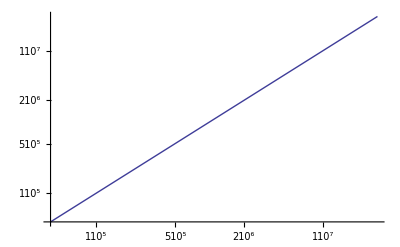

```mathematica
straight=LogLogPlot[x,{x,4 10^4,3 10^7}]
```

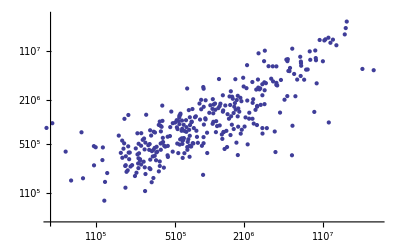

```mathematica
inout=ListLogLogPlot[Table[1000{intrips[[i,2]],outtrips[[i,2]]},{i,Length[intrips]}],PlotRange->{{4 10^4,3 10^7},{4 10^4,3 10^7}}]
```

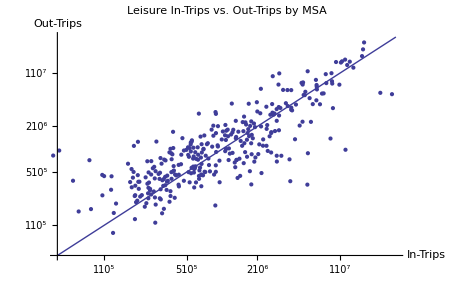

```mathematica
Show[inout,straight,PlotLabel->"Leisure In-Trips vs. Out-Trips by MSA",AxesLabel->{"In-Trips","Out-Trips"}]
```

```mathematica
outinratiomsa=Table[{outtrips[[i,1]],outtrips[[i,2]]/intrips[[i,2]]},{i,Length[intrips]}];
outinratiomsa>>inoutratiomsa;
```

There is a net bias towards out-trips because there are more small MSAs than big ones.  If it were population weighted, the ratio would be unity.

```mathematica
Mean[Table[outinratiomsa[[i,2]],{i,Length[inoutratiomsa]}]]
```

1.5063

Compute renormalized MSA pair trips

```mathematica
leisurepairtrips[[3]]
leisurepairtrips[[3,1,2]]
leisurepairtrips[[3,2]]
inoutratiomsa[[Position[outinratiomsa,leisurepairtrips[[3,1,2]]][[1,1]]]]
inoutratiomsa[[Position[outinratiomsa,leisurepairtrips[[3,1,2]]][[1,1]]]][[1]]
inoutratiomsa[[Position[outinratiomsa,leisurepairtrips[[3,1,2]]][[1,1]]]][[2]]leisurepairtrips[[3,2]]
```

{{40,640},126.876}

640

126.876

{640,0.847612}

640

107.541

```mathematica
renormpairsmsa=Table[If[leisurepairtrips[[i,1,2]]==outinratiomsa[[Position[outinratiomsa,leisurepairtrips[[i,1,2]]][[1,1]]]][[1]],
outinratiomsa[[Position[outinratiomsa,leisurepairtrips[[i,1,2]]][[1,1]]]][[2]]leisurepairtrips[[i,2]],Print["Error"]],{i,Length[leisurepairtrips]}];
```

```mathematica
renormpairsmsa2=Table[{leisurepairtrips[[i,1]],renormpairsmsa[[i]]},{i,Length[renormpairsmsa]}];
```

```mathematica
renormpairsmsa2>>renormpairsmsa;
```

```mathematica
Sum[leisurepairtrips[[i,2]],{i,Length[leisurepairtrips]}]
```

572281.

```mathematica
Sum[renormpairsmsa[[i,2]],{i,Length[renormpairsmsa]}]
```

558791.

```mathematica
Take[leisurepairtrips,10]
```

{{{40,200},8.5145},{{40,450},38.8695},{{40,640},126.876},{{40,840},7.9034},{{40,920},125.346},{{40,1240},19.472},{{40,1920},328.302},{{40,2800},4.5901},{{40,3880},7.9034},{{40,4920},36.7564}}

```mathematica
FileNames[]
```

{150hubpop,2way,3parameterloglinearfit,3parameterloglinearinversewtfit,3parameterloglinearnowtfit,75hubpop,airports,allgrid,arr1,asymodpairsbizplus,asymodpairsbizplusfilter,asympairlist,asypairspeopledistbizplus,ats95allincomes,auto,bizplotpairs,bizspendintensityptsusa04,bizspendintensityusa04,bizstars,bkstail,bts95mma,calibration750,characteristictimes,closebizports,corrmatrix,countmatrix,cumubizspendint,cumuleisspendint,drawusamma,.DS_Store,firmpops,flyratio,fmatrix,fpos,gravdata,hoursvisits,hyperpts,incomespendpts,leisureplotpairs,leisurewealthtrips,measurebar,modeproportions,msadistancetable,msahosp04,msaincomesmod03,msaintrips2000,msaleisuredata,msaleisuredatafilt,msaleisureintrips2000,msaleisureouttrips2000,msaleisurepairtrips2000,msaoccs04,msaoccsmod03,msaocctots04,msaonly,msaouttrips2000,msapops03,msapops0409,msapops48,msapopsmod03,mxvisit,newlistformat,noerrorfilteredflights,nonlinearfitinversewt,nonlinearfitlinearwt,nonlinearfitnowt,nonstops,nozeros,nozeros4k,odpairsbizplus,othertravel,pairspeopledistbizonly,pairspeopledistbizplus,phyloset,physicaljetairports,planeintrosched,planelist,popprodziptable,popzipsums,preplacement,r1ziplist,renormpairsmsa,return1,returnoneways,rmsaleisuredata,statsigprojector,sympairlist,tf,threematrix,tiabiztravbyincome,timearray,totalspend,totaltravel,travelscope06mma,travelscopejetsonleisure,tripsbyhhinccategory,tsimatrixbiz,tsmsa,uniquepositionlist,usa04,usamsa04,usazipsmma,ushubs,wealth,wealthpairs,wealthzips,websurveydata,whatwherewhen,winningregression,zipindices,zzbistars}

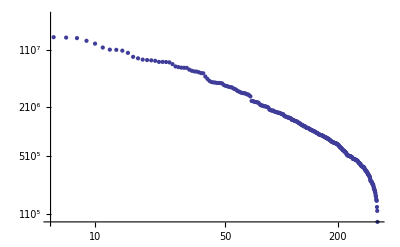

```mathematica
ListLogLogPlot[Sort[Table[1000 outtrips[[i,2]],{i,Length[outtrips]}],#1>#2&]]
```

```mathematica
Sum[leisurepairtrips[[i,2]],{i,Length[leisurepairtrips]}]
```

572281.

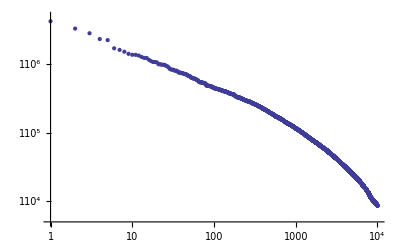

```mathematica
ListLogLogPlot[Take[Sort[Table[1000 leisurepairtrips[[i,2]],{i,Length[leisurepairtrips]}],#1>#2&],10000],PlotRange->{{1,10000},{5000,5000000}}]
```

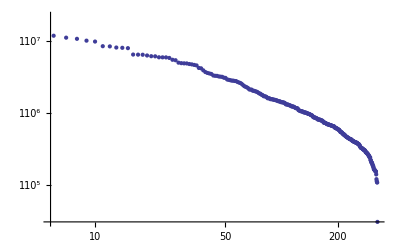

```mathematica
ListLogLogPlot[Sort[Table[1000 leisureouttrips[[i,2]],{i,Length[leisureouttrips]}],#1>#2&]]
```

```mathematica
Length[msapops]
```

328

Delete Anchorage and Honolulu

```mathematica
msapops48=Delete[msapops,{{10},{131}}];
```

Check to see that the TravelScope data and the MSA data are working off the same MSAs

```mathematica
msa03=Table[msapops48[[i,1]],{i,Length[msapops48]}];
Complement[msas,msa03]
Complement[msa03,msas]
```

{}

{}

```mathematica
msapops48>>msapops48;
```

How much of the US population is in MSAs?

```mathematica
usmsapop=Plus@@Table[msapops[[i,4]],{i,Length[msapops]}]
```

215693964

How much of the US population in the lower 48 is in MSAs? (this will be used for proper comparision/calibration with TravelScope)

```mathematica
us48msapop=Plus@@Table[msapops48[[i,4]],{i,Length[msapops48]}]
```

214538131

Look up on Google the US 2003 population

```mathematica
uspop03=294043000
```

294043000

It's a majority, though the Population Reference Bureau claims the urban fraction is 0.77 in 2001.  Perhaps it uses something else than MSAs for this calculation.

```mathematica
msafrac=usmsapop/uspop03//N
```

0.733546

If trips were uniformly distributed in an unbiased fashion, travel between MSAs would be a fraction equal to msafrac^2 of all trips.

```mathematica
msafrac^2
```

0.538089

```mathematica
msaodtrips/alltrips
```

0.452833

Trips originating and ending in MSAs are *underrepresented* with the above hypothesis.  This is as suspected--living in a city means what you need is closer and doesn't require as much long-distance travel to get one's needs met.  Now to find "source" travel law for all travel.  Don't separate biz and leisure initially.  Need MSA origin trips vs. MSA population by MSA.

```mathematica
msas[[1]]
msapops48[[1]]
pairmsas[[1]]
msapops[[Position[msas,pairmsas[[1,1]]][[1,1]],4]]
Length[leisurepairtrips]
leisurepairtrips[[1000]]
msapairdistancetable[[1000]]
leisurepairtrips[[1,1]]
```

40

{40,Abilene, TX,45387,122618}

{40,200}

122618

15633

{{720,2710},12.6575}

{{720,2710},839.783}

{40,200}

Create the master leisure MSA data set comprised of Pop1, Pop2, Dist(1,2), and Travel(1,2).  Then create a filtered dataset that eliminates intra-MSA trips and trips with 2 or fewer data points and trips less than 50 miles in length.

```mathematica
msaleisuredata=Table[{msapops48[[Position[msas,leisurepairtrips[[i,1,1]]][[1,1]],4]],
msapops48[[Position[msas,leisurepairtrips[[i,1,2]]][[1,1]],4]],msapairdistancetable[[i,2]],leisurepairtrips[[i,2]]},{i,Length[leisurepairtrips]}];
```

```mathematica
rmsaleisuredata=Table[{msapops48[[Position[msas,leisurepairtrips[[i,1,1]]][[1,1]],4]],
msapops48[[Position[msas,leisurepairtrips[[i,1,2]]][[1,1]],4]],msapairdistancetable[[i,2]],renormpairsmsa[[i,2]]},{i,Length[leisurepairtrips]}];
```

```mathematica
Dimensions[renormpairsmsa]
```

{15633,2}

```mathematica
msaleisuredata>>msaleisuredata;
```

```mathematica
rmsaleisuredata>>rmsaleisuredata;
```

```mathematica
msaleisuredatafilt=DeleteCases[Table[If[statsigprojector[[i]]==1&& msapairdistancetable[[i,2]]≥50 && leisurepairtrips[[i,2]]≠0,{msapops48[[Position[msas,leisurepairtrips[[i,1,1]]][[1,1]],4]],
msapops48[[Position[msas,leisurepairtrips[[i,1,2]]][[1,1]],4]],msapairdistancetable[[i,2]],leisurepairtrips[[i,2]]},0],{i,Length[leisurepairtrips]}],0];
```

```mathematica
Length[msaleisuredatafilt]
```

4515

```mathematica
msaleisuredatafilt>>msaleisuredatafilt;
```

```mathematica
renormmsaleisuredatafilt=DeleteCases[Table[If[statsigprojector[[i]]==1&& msapairdistancetable[[i,2]]≥50 && leisurepairtrips[[i,2]]≠0,{msapops48[[Position[msas,leisurepairtrips[[i,1,1]]][[1,1]],4]],
msapops48[[Position[msas,leisurepairtrips[[i,1,2]]][[1,1]],4]],msapairdistancetable[[i,2]],renormpairsmsa[[i,2]]},0],{i,Length[leisurepairtrips]}],0];
```

```mathematica
Length[renormmsaleisuredatafilt]
```

4515

```mathematica
Take[renormmsaleisuredatafilt,10]
Take[msaleisuredatafilt,10]
```

{{122618,1073296,190.293,107.541},{122618,3129585,173.189,364.349},{122618,240757,138.565,176.642},{699983,1342488,413.082,32.7225},{699983,7838039,331.752,98.7695},{699983,1632373,205.593,50.073},{699983,1481086,105.804,108.649},{699983,3129585,1018.84,4.67481},{699983,4477977,116.786,113.362},{699983,1432462,1044.02,57.0305}}

{{122618,1073296,190.293,126.876},{122618,3129585,173.189,328.302},{122618,240757,138.565,73.7728},{699983,1342488,413.082,21.1244},{699983,7838039,331.752,75.5243},{699983,1632373,205.593,44.7986},{699983,1481086,105.804,145.933},{699983,3129585,1018.84,4.2123},{699983,4477977,116.786,57.0023},{699983,1432462,1044.02,31.2027}}

Now for the master fit of leisure data:

```mathematica
renormpairsmsa[[3]]
```

{{40,640},107.541}

```mathematica
msaleisuredata[[3]]
```

{122618,1073296,190.293,126.876}

```mathematica
msaleisuredatafilt=<<msaleisuredatafilt;
```

```mathematica
msaleisuredatafilt[[100]]
```

{554432,1417758,971.739,59.7625}

```mathematica
Min[Table[msaleisuredatafilt[[i,4]],{i,Length[msaleisuredatafilt]}]]
```

3.0552

```mathematica
FindFit[Log[msaleisuredatafilt],a + b x + c y + d z, {a,b,c,d},{x,y,z}]
```

{a→0.31332,b→0.291192,c→0.168166,d→-0.473153}

```mathematica
FindFit[Log[renormmsaleisuredatafilt],a + b x + c y + d z, {a,b,c,d},{x,y,z}]
```

{a→-5.10414,b→0.420739,c→0.51231,d→-0.705402}

```mathematica
law=NonlinearModelFit[msaleisuredatafilt, a x^b y^c z^d , {a,b,c,d},{x,y,z}]
```

FittedModel[(0.00623909 x^(«19») y^(«19»))/z^0.689308]

```mathematica
law["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
a | 0.00623909 | 0.00242528 | {0.00148434,0.0109938}
b | 0.571853 | 0.0186643 | {0.535262,0.608444}
c | 0.383041 | 0.0166976 | {0.350306,0.415777}
d | -0.689308 | 0.0208973 | {-0.730277,-0.648339}

```mathematica
Normal[law]
```

(0.00623909 x^0.571853 y^0.383041)/z^0.689308

```mathematica
rlaw=NonlinearModelFit[renormmsaleisuredatafilt, a  x^b  y^c  z^d , {a,b,c,d},{x,y,z}]
```

FittedModel[(0.00013105 x^(«19») y^(«19»))/z^0.822319]

```mathematica
rlaw["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
a | 0.00013105 | 0.0000396329 | {0.0000533496,0.000208749}
b | 0.658904 | 0.0135388 | {0.632361,0.685447}
c | 0.612068 | 0.013002 | {0.586578,0.637558}
d | -0.822319 | 0.0157413 | {-0.853179,-0.791458}

```mathematica
cy Normal[rlaw]//DisplayForm
```

(0.00013105 cy x^0.658904 y^0.612068)/z^0.822319

```mathematica
diagonalplotdata=Table[msaleisuredatafilt[[i,4]]/(.00611 msaleisuredatafilt[[i,1]]^.572 msaleisuredatafilt[[i,2]]^.383 msaleisuredatafilt[[i,3]]^(-.689)),{i,Length[msaleisuredatafilt]}];
Histogram[Log[diagonalplotdata]]
```

-Graphics-

```mathematica
rdiagonalplotdata=Table[renormmsaleisuredatafilt[[i,4]]/(.00013105 renormmsaleisuredatafilt[[i,1]]^.659 renormmsaleisuredatafilt[[i,2]]^.612 renormmsaleisuredatafilt[[i,3]]^(-.822)),{i,Length[renormmsaleisuredatafilt]}];
Histogram[Log[rdiagonalplotdata]]
```

-Graphics-

```mathematica
curvesum=Sum[.00572 msaleisuredatafilt[[i,1]]^.576 msaleisuredatafilt[[i,2]]^.386 msaleisuredatafilt[[i,3]]^(-.697),{i,Length[msaleisuredatafilt]}]
dsum=Sum[msaleisuredatafilt[[i,4]],{i,Length[msaleisuredatafilt]}]
dsum/curvesum .00572
```

382743.

409254.

0.00611621

```mathematica
rcurvesum=Sum[.00013105 renormmsaleisuredatafilt[[i,1]]^.659 renormmsaleisuredatafilt[[i,2]]^.612 renormmsaleisuredatafilt[[i,3]]^(-.822),{i,Length[renormmsaleisuredatafilt]}]
rdsum=Sum[renormmsaleisuredatafilt[[i,4]],{i,Length[renormmsaleisuredatafilt]}]
```

359548.

377167.

```mathematica
rdsum/rcurvesum  .00013105
```

0.000137472

Check to see that we're using the same MSAs in this calculation from TravelScope data and MSA data

```mathematica
Do[If[msapops48[[i,1]]≠outtrips[[i,1]],Print[i]],{i,Length[msas]}]
```

Create the dataset of MSA population versus out-travel from each MSA to find functional dependence, do nonlinear fit, measure log variance

```mathematica
poptraveldata=Sort[Table[{msapops48[[i,4]],1000 outtrips[[i,2]]},{i,1,Length[msapops48]}]];
```

```mathematica
nlmfit=NonlinearModelFit[poptraveldata, a x^(b) , {a,b,c},x,Weights->Table[poptraveldata[[i,2]],{i,1,326}]]
fn=Normal[nlmfit]
Sum[Log[poptraveldata[[i,2]]/nlmfit[poptraveldata[[i,1]]]]^2,{i,326}]
```

FittedModel[91.7621 x^0.775954]

91.7621 x^0.775954

162.314

```mathematica
LinearModelFit[Log[poptraveldata],{0,x},x,Weights->Table[poptraveldata[[i,2]],{i,1,326}]]
```

FittedModel[1.96059+0.945627 x]

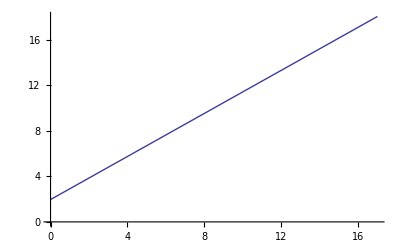

```mathematica
line=Plot[1.96+.945 x, {x,0,17}]
```

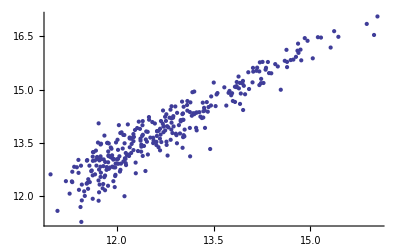

```mathematica
points=ListPlot[Log[poptraveldata]]
```

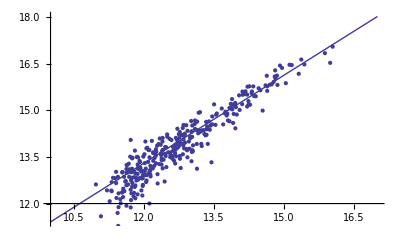

```mathematica
Show[line,points]
```

```mathematica
leisurepoptraveldata=Sort[Table[{msapops48[[i,4]],1000 leisureouttrips[[i,2]]},{i,1,Length[msapops48]}]];
```

```mathematica
nlmfit=NonlinearModelFit[leisurepoptraveldata, a x^b Exp[-c/x] , {a,b,c},x,Weights->Table[leisurepoptraveldata[[i,1]]^(-1),{i,1,326}]]
fn=Normal[nlmfit]//StandardForm
Sum[Log[leisurepoptraveldata[[i,2]]/nlmfit[leisurepoptraveldata[[i,1]]]]^2 ,{i,326}]
Sum[(leisurepoptraveldata[[i,2]]-nlmfit[leisurepoptraveldata[[i,1]]])^2,{i,326}]
```

FittedModel[9.1656 ⅇ^(-«18»/x) x^0.914985]

9.1656 ⅇ^(-23758.2/x) x^0.914985

53.7932

1.83063×10^14

```mathematica
Exp[Sqrt[72.9/326]]
```

1.60462

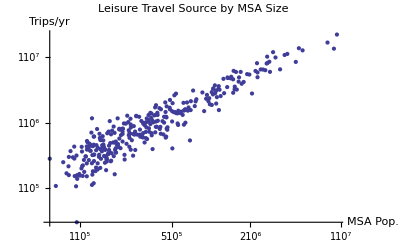

```mathematica
traveldataplot=ListLogLogPlot[leisurepoptraveldata,PlotLabel->"Leisure Travel Source by MSA Size",AxesLabel->{"MSA Pop.", "Trips/yr"}]
```

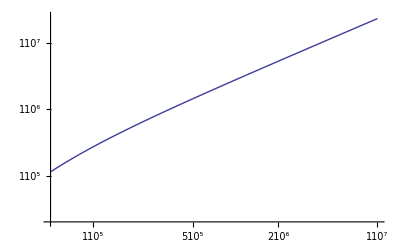

```mathematica
powerlawfit=LogLogPlot[fn,{x,5 10^4,10^7},PlotRange->{{5 10^4, 10^7},{2 10^4, 2.5 10^7}}]
```

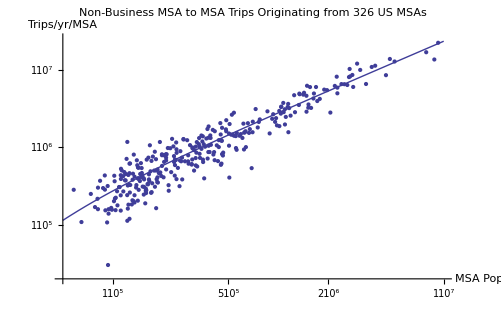

```mathematica
Show[powerlawfit,traveldataplot,PlotLabel->"Non-Business MSA to MSA Trips Originating from 326 US MSAs",AxesLabel->{"MSA Pop", "Trips/yr/MSA"}]
```

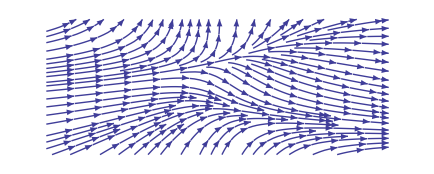

```mathematica
StreamPlot[-{-1-x^2+y/3,1+x-y^2},{x,-4,4},{y,-3,3},AspectRatio->.4, Frame->False]
```

## Functions for filtering data

Note:  Original versions of the following functions all had a cutoff at 100 miles for DayJet purposes, but 50 miles is more useful for long distance travel generation purposes.

FIlters for leisure travel with precise zipcode destination

```mathematica
leisureexact[region_,lowerbound_,upperbound_]:={
ldist=Table[0, {k,Length[region]}];
j=1;
Do[
{
If[(region[[i,6]]>6 ||region[[i,6]]<4) && region[[i,48]]≥lowerbound && region[[i,48]]≤upperbound && region[[i,33]]=="Zip2003" && region[[i,45]]=="Zip2003", ldist[[j]]={region[[i,1]],region[[i,6]],region[[i,7]],region[[i,8]],region[[i,9]],region[[i,17]],region[[i,22]], region[[i,23]], region[[i,25]] +region[[i,26]], region[[i,41]],region[[i,48]], region[[i,46]],region[[i,47]]}],
j+=1;
},{i,Length[region]}
],
ldist=DeleteCases[ldist,0];
}
```

Leisure travel with both precise and inprecise destination

```mathematica
leisureall[region_,lowerbound_,upperbound_]:={
ldist=Table[0, {k,Length[region]}];
j=1;
Do[
{
If[(region[[i,6]]>6 ||region[[i,6]]<4)  && region[[i,48]]≥lowerbound && region[[i,48]]≤ upperbound, ldist[[j]]={region[[i,1]],region[[i,6]],region[[i,7]],region[[i,8]],region[[i,9]],region[[i,17]],region[[i,22]], region[[i,23]], region[[i,25]] +region[[i,26]], region[[i,41]],region[[i,48]], region[[i,46]],region[[i,47]]}],
j+=1;
},{i,Length[region]}
],
ldist=DeleteCases[ldist,0];
}
```

Biz travel with precise zipcode destination

```mathematica
bizexact[region_,lowerbound_,upperbound_]:={
bdist=Table[0, {k,Length[region]}];
j=1;
Do[
{
If[(region[[i,6]]==4 || region[[i,6]]==5||region[[i,6]]==6)&& region[[i,48]]≥lowerbound && region[[i,48]]≤upperbound && region[[i,33]]=="Zip2003" &&region[[i,45]]=="Zip2003", bdist[[j]]={region[[i,1]],region[[i,6]],region[[i,7]],region[[i,8]],region[[i,9]],region[[i,17]],region[[i,22]], region[[i,23]], region[[i,25]] +region[[i,26]], region[[i,41]],region[[i,48]], region[[i,46]],region[[i,47]]}],
j+=1;
},{i,Length[region]}
],
bdist=DeleteCases[bdist,0];
}
```

Biz travel with precise and imprecise destination

```mathematica
bizall[region_,lowerbound_,upperbound_]:={
bdist=Table[0, {k,Length[region]}];
j=1;
Do[
{
If[(region[[i,6]]==4 || region[[i,6]]==5||region[[i,6]]==6)&& region[[i,48]]≥lowerbound && region[[i,48]]≤ upperbound, bdist[[j]]={region[[i,1]],region[[i,6]],region[[i,7]],region[[i,8]],region[[i,9]],region[[i,17]],region[[i,22]], region[[i,23]], region[[i,25]] +region[[i,26]], region[[i,41]],region[[i,48]], region[[i,46]],region[[i,47]]}],
j+=1;
},{i,Length[region]}
],
bdist=DeleteCases[bdist,0];
}
```

Filter for precise geographical destination and purpose of trip

```mathematica
exactdestinationpurpose[region_,index_]:={
edist=Table[0, {k,Length[region]}];
j=1;
Do[
{
If[region[[i,6]]==index  && region[[i,45]]=="Zip2003", edist[[j]]={region[[i,1]],region[[i,6]],region[[i,7]],region[[i,8]],region[[i,9]],region[[i,17]],region[[i,22]], region[[i,23]], region[[i,25]] +region[[i,26]], region[[i,41]],region[[i,43]],region[[i,48]]}],
j+=1;
},{i,Length[region]}
],
edist=DeleteCases[edist,0];
Length[edist]
}
```

```mathematica
Length[Sort[Tally[Table[edist[[i,11]],{i,Length[edist]}]],#1[[2]]>#2[[2]]&]]
```

1717

Prepare to do some vector algebra--compute dot products in a 5k-dimensional "travel characterization" space using zipcodes as basis vectors

```mathematica
zipvectorbasis=Table[If[usa04[[i,45]]=="Zip2003", usa04[[i,43]],0],{i,Length[usa04]}];
zipvectorbasis=Union[DeleteCases[zipvectorbasis,0]];
Length[zipvectorbasis]
```

5231

```mathematica
Plus@@Flatten[tripvectormatrix]
```

685005.

```mathematica
tripvectormatrix=Table[0,{8},{5231}];

Do[
If[
usa04[[i,45]]=="Zip2003" && usa04[[i,6]]≠0, 
tripvectormatrix[[usa04[[i,6]],Position[zipvectorbasis,usa04[[i,43]]][[1,1]]]]+=usa04[[i,41]]
],{i,Length[usa04]}]
```

```mathematica
dotproducts=Table[Table[tripvectormatrix[[i,p]],{p,1,5231}].Table[tripvectormatrix[[j,q]],{q,1,5231}]/
(Norm[Table[tripvectormatrix[[i,p]],{p,1,5231}]] Norm[Table[tripvectormatrix[[j,q]],{q,1,5231}]]),{i,8},{j,8}]//MatrixForm
```

(1. | 0.518881 | 0.701954 | 0.828792 | 0.832125 | 0.891937 | 0.789254 | 0.777495
0.518881 | 1. | 0.488433 | 0.476219 | 0.407091 | 0.367671 | 0.636257 | 0.480025
0.701954 | 0.488433 | 1. | 0.804229 | 0.800169 | 0.620321 | 0.841944 | 0.717046
0.828792 | 0.476219 | 0.804229 | 1. | 0.876799 | 0.826594 | 0.801824 | 0.750413
0.832125 | 0.407091 | 0.800169 | 0.876799 | 1. | 0.873129 | 0.770372 | 0.77452
0.891937 | 0.367671 | 0.620321 | 0.826594 | 0.873129 | 1. | 0.671749 | 0.736737
0.789254 | 0.636257 | 0.841944 | 0.801824 | 0.770372 | 0.671749 | 1. | 0.748202
0.777495 | 0.480025 | 0.717046 | 0.750413 | 0.77452 | 0.736737 | 0.748202 | 1.)

```mathematica
leisureall[usa04,100,3000];
bizall[usa04,100,3000];
```

```mathematica
Dimensions[ldist]
Dimensions[bdist]
```

{68604,13}

{24064,13}

```mathematica
leisureexact[usa04,100,3000];
bizexact[usa04,100,3000];
```

```mathematica
Dimensions[ldist]
 Dimensions[bdist]
```

{30369,13}

{9719,13}

```mathematica
l
```

```mathematica
ldist[[1,11]]
```

517.227

```mathematica
bdistfly=DeleteCases[Table[If[bdist[[i,4]]≠5,0,bdist[[i]]],{i,Length[bdist]}],0];
ldistfly=DeleteCases[Table[If[ldist[[i,4]]≠5,0,ldist[[i]]],{i,Length[ldist]}],0];
```

```mathematica
bsort=Sort[bdistfly,#2[[11]]<#1[[11]]&];
lsort=Sort[ldistfly,#2[[11]]<#1[[11]]&];
```

```mathematica
Length[lsort]
```

6363

```mathematica
lsort[[3181]]
```

{61628-3134231-A,1,0,5,0,22,8,20,1,4.9073,1033.58,-94.4162,35.364}

```mathematica
bsort[[4859]]
```

{52307-2716021-A,4,0,1,0,3,4,85,2,7.9553,343.782,-121.487,38.5772}

```mathematica
ldist[[2]]
```

{27-0312761-A,1,0,1,0,22,3,100,1,4.9596,185.844,-94.7706,47.5275}

```mathematica
avgdist[datalist_]:=Sum[datalist[[i,10]] datalist[[i,11]],{i,Length[datalist]}]/Sum[datalist[[i,10]],{i,Length[datalist]}]
```

```mathematica
avgflydist[datalist_]:=Sum[If[datalist[[i,4]]==5,datalist[[i,10]] datalist[[i,11]],0],{i,Length[datalist]}]/Sum[If[datalist[[i,4]]==5,datalist[[i,10]],0],{i,Length[datalist]}]
```

```mathematica
avgdist[ldist]
```

465.842

```mathematica
avgflydist[ldist]
```

1162.91

## Notes

Average length of a leisure trip with lower cutoff of 50 mi:  376 miles
Average length of a business trip with lower cutoff of 50 mi:  479 miles
Average length of a leisure trip with lower cutoff of 100 mi: 465 mi.
Average length of a business trip with lower cutoff of 100 mi: 570 mi.
Average length of a flown leisure trip, cutoff= 100 mi:  1163 mi
Average length of a flown biz trip, cutoff = 100 mi, 963 mi
All the above calculated using "Exact" algorithm
Using "All' makes at most 3% difference.
Median leisure trip is 274.3 mi.
Median biz trip is 343.8 mi.
Median flown biz trip: 743 mi.
Median flown leisure trip: 1034 mi.

## Analysis and Graphics

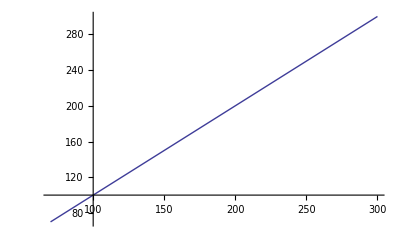
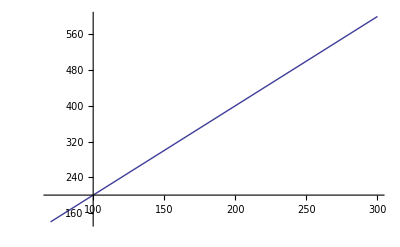
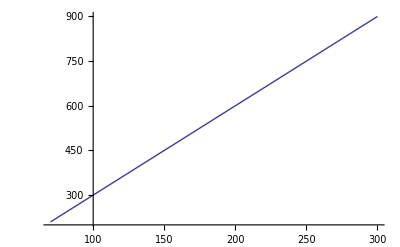

```mathematica
g=Table[Plot[.75 10^6 (1.08^(5 i))/x^2,{x,70,300},PlotRange->{{70,300},{100,600}}],{i,2,8}];
t=Table[Plot[i x,{x,70,300}],{i,3}]
```

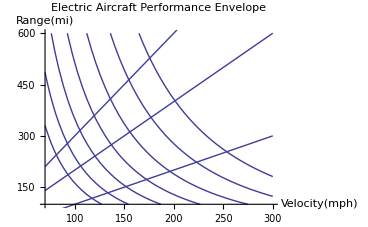

```mathematica
Show[{g,t},PlotLabel->"Electric Aircraft Performance Envelope",AxesLabel->{"Velocity(mph)","Range(mi)"},AxesOrigin->{70,100}]
```

```mathematica
flybiztriptranches=Table[{100 i , 0},{i,26}];
Do[
{bizall[usa04,100 m,100 m + 100];
trips=Sum[If[bdist[[p,4]]==5,bdist[[p,10]],0],{p,Length[bdist]}];
flybiztriptranches[[m,2]]=trips;
},
{m,26}
]
```

```mathematica
flybiztriptranches
```

{{100,4606.33},{200,9778.18},{300,10034.8},{400,7601.09},{500,7313.65},{600,7131.99},{700,6612.01},{800,6061.45},{900,6347.92},{1000,4497.53},{1100,3428.61},{1200,3046.73},{1300,2337.69},{1400,2894.7},{1500,2567.28},{1600,2025.71},{1700,2185.34},{1800,1881.07},{1900,1991.03},{2000,1141.69},{2100,1785.44},{2200,1662.93},{2300,2101.19},{2400,2123.6},{2500,1448.42},{2600,387.455}}

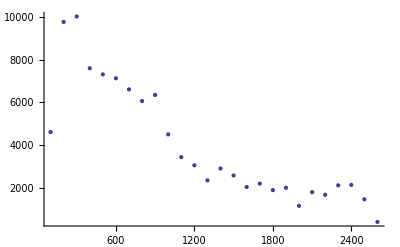

```mathematica
ListPlot[flybiztriptranches]
```

```mathematica
flyleistriptranches=Table[{100 i , 0},{i,26}];
Do[
{leisureexact[usa04,100 m,100 m + 99.99];
trips=Sum[If[ldist[[p,4]]==5,ldist[[p,10]],0],{p,Length[ldist]}];
 flyleistriptranches[[m,2]]=trips;
},
{m,26}
]
```

```mathematica
noflyleistriptranches=Table[{100 i , 0},{i,26}];
Do[
{leisureexact[usa04,100 m,100 m + 99.99];
trips=Sum[If[ldist[[p,4]]!=5,ldist[[p,10]],0],{p,Length[ldist]}];
noflyleistriptranches[[m,2]]=trips;
},
{m,26}
]
```

```mathematica
leisureflyfactor=151444000/67524;
```

```mathematica
noflyleistriptranches
```

{{100,148948.},{200,74395.3},{300,34632.2},{400,20175.5},{500,14033.8},{600,9630.52},{700,6458.84},{800,5033.6},{900,4068.67},{1000,2942.76},{1100,2249.12},{1200,1601.07},{1300,1158.35},{1400,816.737},{1500,931.325},{1600,623.777},{1700,462.339},{1800,567.258},{1900,482.772},{2000,541.857},{2100,256.984},{2200,307.231},{2300,244.961},{2400,244.868},{2500,133.797},{2600,43.9043}}

```mathematica
flyleistriptranches
```

{{100,1272.25},{200,2720.53},{300,3549.75},{400,2711.22},{500,3981.59},{600,4644.78},{700,3853.68},{800,3904.27},{900,5383.28},{1000,4995.28},{1100,3482.22},{1200,2918.74},{1300,2143.75},{1400,2086.49},{1500,2276.91},{1600,2150.78},{1700,2517.94},{1800,1744.27},{1900,1640.43},{2000,1508.29},{2100,1887.16},{2200,1971.06},{2300,1581.15},{2400,1381.21},{2500,963.891},{2600,253.033}}

```mathematica
leisureflyproportion=Table[{100 i, flyleistriptranches[[i,2]]/(flyleistriptranches[[i,2]]+noflyleistriptranches[[i,2]])},{i,26}]
```

{{100,0.00846925},{200,0.0352785},{300,0.0929692},{400,0.118462},{500,0.22101},{600,0.325372},{700,0.373689},{800,0.436823},{900,0.569542},{1000,0.629283},{1100,0.607576},{1200,0.645766},{1300,0.649209},{1400,0.71868},{1500,0.709708},{1600,0.775179},{1700,0.844867},{1800,0.754596},{1900,0.77262},{2000,0.735699},{2100,0.880146},{2200,0.865148},{2300,0.865856},{2400,0.849412},{2500,0.87811},{2600,0.852143}}

```mathematica
FindFit[leisureflyproportion, a- Exp[-b x],{a,b},x]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

FindFit::nrlnum: The function value « 1 » is not a list of real numbers with dimensions {26} at {a, b} = {0.6082858258410606`, -1.612377214707145`*^41}.

{a→0.608286,b→-1.61238×10^41}

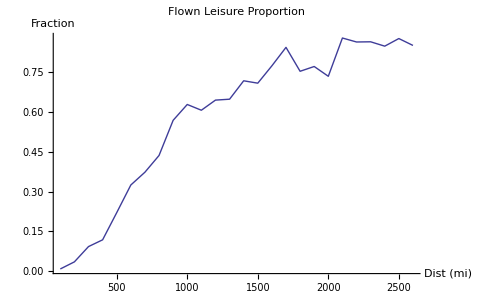

```mathematica
ListPlot[leisureflyproportion, Joined->True, PlotLabel->"Flown Leisure Proportion",AxesLabel->{"Dist (mi)", "Fraction"}]
```

```mathematica
flyleistriptranches=Table[{100 i , 0},{i,26}];
Do[
{leisureall[usa04,100 m,100 m + 99.99];
trips=Sum[If[ldist[[p,4]]==5,ldist[[p,10]],0],{p,Length[ldist]}];
flyleistriptranches[[m,2]]=trips;
},
{m,26}
]
```

```mathematica
flyleistriptranches
```

{{100,3882.23},{200,6408.76},{300,8482.15},{400,7936.72},{500,8381.01},{600,9782.81},{700,8664.82},{800,10278.1},{900,12237.3},{1000,11701.9},{1100,7414.66},{1200,5916.3},{1300,4729.48},{1400,4485.82},{1500,4622.46},{1600,4464.2},{1700,4781.81},{1800,3636.37},{1900,3632.03},{2000,2737.12},{2100,3385.86},{2200,3296.76},{2300,3272.03},{2400,3828.88},{2500,2634.05},{2600,850.633}}

```mathematica
Sum[flyleistriptranches[[i,2]],{i,Length[flyleistriptranches]}]
```

67524.

```mathematica
Sum[flyleistriptranches[[i,2]],{i,Length[flyleistriptranches]}]
```

151444.

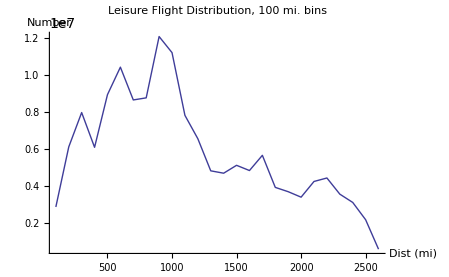

```mathematica
ListPlot[flyleistriptranches,Joined->True,PlotLabel->"Leisure Flight Distribution, 100 mi. bins", AxesLabel->{"Dist (mi)", "Number"}]
```

```mathematica
cumulflybiztrip=Table[{50 i , 0},{i,52}];
Do[
{bizall[usa04,50m,3000];
trips=Sum[If[bdist[[p,4]]==5,bdist[[p,10]],0],{p,Length[bdist]}];
cumulflybiztrip[[m,2]]=1000  trips;
},
{m,52}
]
```

```mathematica
cumulflyleisuretrip=Table[{50 i , 0},{i,52}];
Do[
{leisureall[usa04,50m,3000];
trips=Sum[If[ldist[[p,4]]==5,ldist[[p,10]],0],{p,Length[ldist]}];
cumulflyleisuretrip[[m,2]]=1000  trips;
},
{m,52}
]
```

```mathematica
cumuldrivebiztrip=Table[{50 i , 0},{i,52}];
Do[
{bizall[usa04,50 m,3000];
trips=Sum[If[bdist[[p,4]]!=5,bdist[[p,10]],0],{p,Length[bdist]}];
cumuldrivebiztrip[[m,2]]=1000  trips;
},
{m,52}
]
```

```mathematica
cumuldriveleisuretrip=Table[{50 i , 0},{i,52}];
Do[
{leisureall[usa04,50 m,3000];
trips=Sum[If[ldist[[p,4]]!=5,ldist[[p,10]],0],{p,Length[ldist]}];
cumuldriveleisuretrip[[m,2]]=1000  trips;
},
{m,52}
]
```

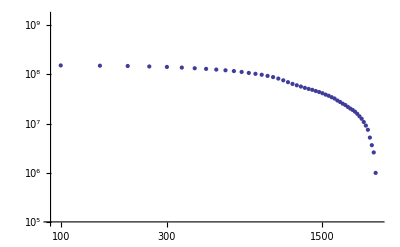

```mathematica
fl=ListLogLogPlot[cumulflyleisuretrip,PlotRange->{{90,2650},{10^5, 1.5 10^9}}]
```

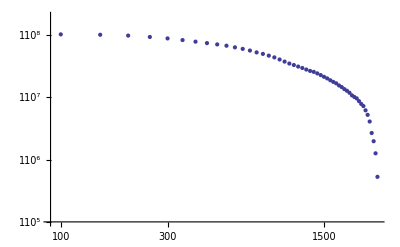

```mathematica
fb=ListLogLogPlot[cumulflybiztrip,PlotRange->{{90,2600},{10^5, 2 10^8}}]
```

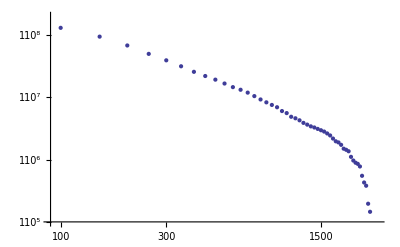

```mathematica
db=ListLogLogPlot[cumuldrivebiztrip, PlotRange->{{90,2700},{10^5, 2 10^8}}]
```

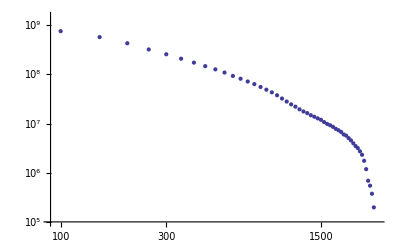

```mathematica
dl=ListLogLogPlot[cumuldriveleisuretrip, PlotRange->{{90,2700},{10^5, 1.5 10^9}}]
```

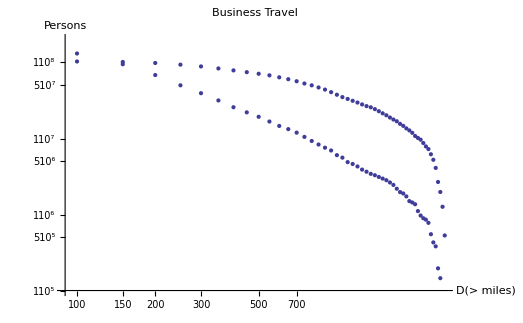

```mathematica
Show[fb,db, PlotLabel->"Business Travel", AxesLabel->{"D(> miles)", "Persons"}]
```

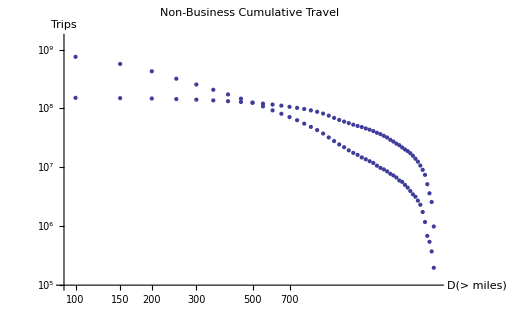

```mathematica
Show[fl,dl, PlotLabel->"Non-Business Cumulative Travel", AxesLabel->{"D(> miles)", "Trips"}]
```

```mathematica
tripsgreaterthan=Table[{50 i, 0},{i,54}];
Do[
{bizexact[usa04,50 m,3000];
trips=Sum[bdist[[p,10]],{p,Length[bdist]}];
tripsgreaterthan[[m,2]]=trips;
},
{m,54}
]
```

```mathematica
tripsgreaterthan
```

{{50,116825.},{100,95306.4},{150,77776.},{200,64960.1},{250,55333.3},{300,49198.3},{350,44450.8},{400,40006.5},{450,36967.},{500,34315.2},{550,31921.4},{600,29641.1},{650,27506.8},{700,25434.6},{750,23415.6},{800,21785.7},{850,20367.6},{900,18946.7},{950,17662.8},{1000,16370.9},{1050,15284.1},{1100,14306.},{1150,13463.8},{1200,12859.9},{1250,12074.1},{1300,11578.6},{1350,11204.9},{1400,10694.2},{1450,10101.2},{1500,9355.86},{1550,8798.36},{1600,8295.27},{1650,7825.33},{1700,7303.25},{1750,6897.46},{1800,6541.01},{1850,6108.26},{1900,5679.6},{1950,5242.17},{2000,4733.43},{2050,4446.11},{2100,4052.39},{2150,3706.73},{2200,3359.08},{2250,3040.22},{2300,2505.9},{2350,2071.6},{2400,1458.46},{2450,864.797},{2500,649.17},{2550,408.179},{2600,277.97},{2650,215.12},{2700,133.403}}

```mathematica
Length[ldist]
```

30369

```mathematica
Sum[ldist[[p,10]],{p,Length[ldist]}]
```

398627.

```mathematica
Sum[bdist[[p,10]],{p,Length[bdist]}]
```

234431.

```mathematica
tgt=Table[{tripsgreaterthan[[i,1]],904767000/398627  tripsgreaterthan[[i,2]]},{i,54}];
```

```mathematica
bgt=Table[{tripsgreaterthan[[i,1]],234431000/95306  tripsgreaterthan[[i,2]]},{i,54}];
```

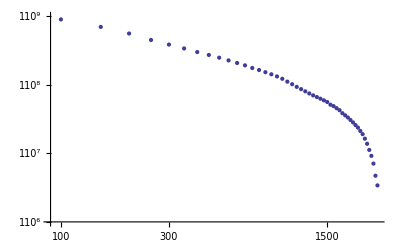

```mathematica
cumul=ListLogLogPlot[Take[tgt,{2,50}],PlotRange->{{90,2500},{10^6,10^9}}]
```

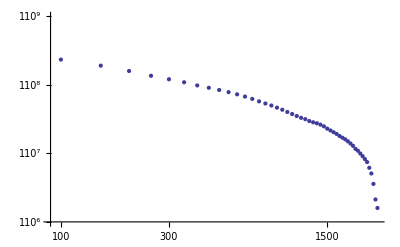

```mathematica
cumul2=ListLogLogPlot[Take[bgt,{2,50}],PlotRange->{{90,2500},{10^6,1 10^9}}]
```

```mathematica
FindFit[Take[tgt,{2,16}],a x^b, {a,b},x]
```

{a→4.01621×10^10,b→-0.815974}

```mathematica
Solve[x^(-.816)==.5,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2.33835}}

```mathematica
Integrate[x^(1-.649),{x,100,1500}]/Integrate[x^(-.649),{x,100,1500}]
```

618.895

```mathematica
bgt
```

{{50,2.87363×10^8},{100,2.34432×10^8},{150,1.91311×10^8},{200,1.59787×10^8},{250,1.36107×10^8},{300,1.21016×10^8},{350,1.09339×10^8},{400,9.84067×10^7},{450,9.09303×10^7},{500,8.44076×10^7},{550,7.85193×10^7},{600,7.29103×10^7},{650,6.76604×10^7},{700,6.25634×10^7},{750,5.7597×10^7},{800,5.35878×10^7},{850,5.00996×10^7},{900,4.66046×10^7},{950,4.34465×10^7},{1000,4.02686×10^7},{1050,3.75954×10^7},{1100,3.51895×10^7},{1150,3.3118×10^7},{1200,3.16323×10^7},{1250,2.96995×10^7},{1300,2.84807×10^7},{1350,2.75614×10^7},{1400,2.63054×10^7},{1450,2.48466×10^7},{1500,2.30133×10^7},{1550,2.16419×10^7},{1600,2.04045×10^7},{1650,1.92485×10^7},{1700,1.79643×10^7},{1750,1.69662×10^7},{1800,1.60894×10^7},{1850,1.50249×10^7},{1900,1.39705×10^7},{1950,1.28945×10^7},{2000,1.16432×10^7},{2050,1.09364×10^7},{2100,9.96795×10^6},{2150,9.11771×10^6},{2200,8.26257×10^6},{2250,7.47826×10^6},{2300,6.16395×10^6},{2350,5.09565×10^6},{2400,3.58747×10^6},{2450,2.1272×10^6},{2500,1.59681×10^6},{2550,1.00403×10^6},{2600,683744.},{2650,529145.},{2700,328141.}}

```mathematica
FindFit[Take[bgt,{2,14}],a x^b,{a,b},x]
```

{a→4.79128×10^9,b→-0.64866}

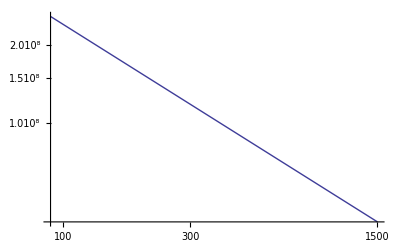

```mathematica
bpowerlawfit=LogLogPlot[4.79 10^9 x^(-.649),{x,90,1500}]
```

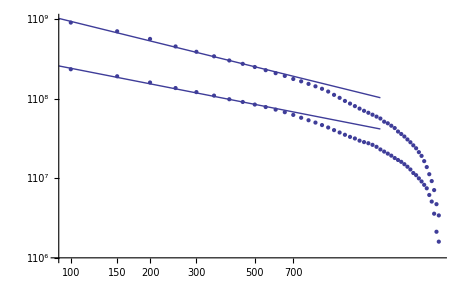

```mathematica
Show[cumul2,cumul,powerlawfit,bpowerlawfit]
```

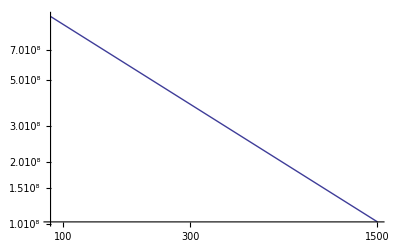

```mathematica
powerlawfit=LogLogPlot[4.016 10^10 x^(-.816),{x,90,1500}]
```

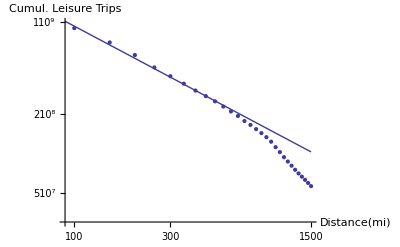

```mathematica
Show[cumul,powerlawfit,AxesLabel->{"Distance(mi)","Cumul. Leisure Trips"}]
```

## Extract a Travel Law

Need to factor in an "uplift" for all of the information that was only provided at the state level but that will not be used to determine precise travel patterns.

```mathematica
ld=<<travelscopejetsonleisure;
```

```mathematica
Sum[ldist[[i,10]],{i,Length[ldist]}]
```

1.17419×10^6

```mathematica
Sum[bdist[[i,10]],{i,Length[bdist]}]
```

327774.

```mathematica
Sum[ldist[[i,10]],{i,Length[ldist]}]
```

504168.

```mathematica
multiplier=719013/504168//N
```

1.42614

```mathematica
ldist>>travelscopejetsonleisure;
```

```mathematica
Sum[ldist[[i,10]],{i,Length[ldist]}]
```

504168.

```mathematica
ldist[[1]]
```

{8-0306561-A,1,0,5,0,28,0,,4,24.1532,517.227,-79.8246,34.2079}

```mathematica
<<"BarCharts`";<<"Histograms`"
```

```mathematica
make3dplot[resolutiondegrees_,datalist_]:={
height=26/resolutiondegrees;
width=60/resolutiondegrees;
datatable=Table[0,{i,height},{j,width}];
Do[{ycoord=Floor[(125+datalist[[i,12]])/resolutiondegrees]+1,
xcoord=Floor[(datalist[[i,13]]-24)/resolutiondegrees]+1,
datatable[[xcoord,ycoord]]+=datalist[[i,10]]},{i,Length[datalist]}];
}
```

```mathematica
make3dplot[.25,ldist]
```

{Null}

```mathematica
Dimensions[datatable]
```

{104,240}

```mathematica
leisurelist=Flatten[datatable,1];
```

General::spell1: Possible spelling error: new symbol name "leisurelist" is similar to existing symbol "leisuredist". More…

```mathematica
Dimensions[leisurelist]
```

{24960}

```mathematica
sll=Sort[leisurelist,#2[[2]]<#1[[2]]&];
```

Part::partd: Part specification 0 ⟦ 2 ⟧ is longer than depth of object. More…

General::stop: Further output of Part :: "partd" will be suppressed during this calculation. More…

```mathematica
datarange=1206
```

1206

```mathematica
logtable=Table[{i,1.426 sll[[i]]},{i,2255}];
```

```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

```mathematica
logleisurerank3=ListLogLogPlot[logtable,PlotRange->{{0.9,2000},{3,13000}}]
```

⁃Graphics⁃

```mathematica
both=Show[logleisurerank,logleisurerank3]
```

⁃Graphics⁃

```mathematica
Export["LeisureAndBizRank.png",both,ImageResolution->225];
```

```mathematica
Plus@@leisurelist
```

504168.

```mathematica
leislogdata=logdata;
```

```mathematica
bislogdata=logdata;
```

```mathematica
leisurequotient=(leislogdata+1)/(bislogdata+1.5);
```

```mathematica
logdata=Log[datatable+1];
```

```mathematica
blplot=ListDensityPlot[leisurequotient, AspectRatio->.75,ColorFunction->Hue,Mesh->False,FrameTicks->None]
```

General::spell: Possible spelling error: new symbol name "blplot" is similar to existing symbols {bplot, lplot}. More…

⁃DensityGraphics⁃

```mathematica
lplotd=Graphics[DensityGraphics[lplot]]
```

⁃Graphics⁃

```mathematica
p3=Show[{blplot,a},PlotRange->{{0,240},{0,104}},AspectRatio->.65]
```

⁃Graphics⁃

```mathematica
SetDirectory["/Users/brucesawhill/Desktop"]
```

/Users/brucesawhill/Desktop

```mathematica
Export["LeisureQuotientPlot.png", p3,ImageResolution->250];
```

These filters are to remove data entries that do not give trip cost or duration information and hence can't be used to compute spending intensity.

```mathematica
leisfilt=DeleteCases[Table[If[leisdist[[i,6]]==""||leisdist[[i,5]]=="--" || leisdist[[i,6]]=="-----",0,leisdist[[i]]],{i,Length[ldist]}],0];
```

```mathematica
bizfilt=DeleteCases[Table[If[bdist[[i,6]]==""||bdist[[i,5]]=="--" || bdist[[i,6]]=="-----",0,bdist[[i]]],{i,Length[bdist]}],0];
```

General::spell1: Possible spelling error: new symbol name "bfilt1" is similar to existing symbol "filt1".

Count the number of data points that are within the Jetson distance range.

```mathematica
totaldatapts[region_]:={
j=0;
numpeople=0;
Do[ {j+=1, numpeople+=region[[i,10]]},{i,Length[region]}];
j,
numpeople
}
```

```mathematica
<<Statistics`DataManipulation`
```

```mathematica
zipfreqtable=Reverse[Sort[Tally[Table[ldist⟦i,13⟧,{i,Length[ldist]}]]],2];
```

```mathematica
Sort[zipfreqtable,#2[[2]]>#1[[2]]&];
```

```mathematica
topleisuredestinationzips=Take[Sort[Reverse[Sort[Tally[Table[ldist⟦i,13⟧,{i,Length[ldist]}]]],2]],-300];
```

```mathematica
topleisuredestinationzips>>topleisuredestinationzips;
```

```mathematica
filt2=filt1;
```

```mathematica
leisurewealthtrips=DeleteCases[Table[If[filt2[[i,6]]/(filt2[[i,5]] filt2[[i,7]])>300 && filt2[[i,9]]≥150 && filt2[[i,9]]<600,filt2[[i]],0],{i,Length[filt2]}],0];
```

```mathematica
Length[leisurewealthtrips]
```

2569

```mathematica
numwealthtrips=Sum[leisurewealthtrips[[i,8]]
 leisurewealthtrips[[i,7]] ,{i,Length[leisurewealthtrips]}]
```

```mathematica
numfly=Sum[If[leisurewealthtrips[[i,2]]==5,leisurewealthtrips[[i,8]]
 leisurewealthtrips[[i,7]],0]  ,{i,Length[leisurewealthtrips]}]
```

3312.1

```mathematica
avgwealthtripdistance=Sum[leisurewealthtrips[[i,8]]
 leisurewealthtrips[[i,7]] leisurewealthtrips[[i,9]] ,{i,Length[leisurewealthtrips]}]/numwealthtrips
```

1043.62

```mathematica
leisurewealthtrips>>leisurewealthtrips;
```

```mathematica
Sum[usa04[[i,41]], {i,Length[usa04]}]
```

1.50197×10^6

```mathematica
Sum[bdist[[i,8]]  ,{i,Length[bdist]}]
```

218368.

```mathematica
origdestusa=Table[{usa04⟦i,5⟧,usa04⟦i,43⟧},{i,Length[usa04]}];
usaflat=Flatten[%];
popularzips=Sort[Reverse[Sort[Tally[usaflat]],2],#2⟦1⟧<#1⟦1⟧&];
greaterthanten=Take[popularzips,6000];
popularzips=DeleteCases[Table[If[Mod[greaterthanten⟦i,2⟧,100]≠0,greaterthanten⟦i,2⟧,0],{i,2,Length[greaterthanten]}],0];
Export["popularzips.txt",popularzips,"Table"];
```

```mathematica
usa04=<<usa04;
```

```mathematica
Dimensions[bdist]
```

{18545,11}

```mathematica
householdbyincomesums[dataset_,classlist__]:=Sum[If[MemberQ[classlist,dataset[[i,4]]],1,0] dataset[[i,8]],{i,Length[dataset]}]
```

```mathematica
householdbyincomesums[bdist,{1,2,3,4}]
```

8343.89

Since the highest income category (Number 35) is $300k and higher, use the IRS data to figure out a mean.  An upper limit on the income integration of $1.5M/yr yields about $500k.  An upper limit of $10M/yr. yields $600k, probably too rich for JSC.

```mathematica
NIntegrate[x^(-1.942),{x,300,1500}]/NIntegrate[x^(-2.942),{x,300,1500}]
```

504.844

```mathematica
incomecenters={6.25,8.75,11.25,13.75,16.25,18.75,21.25,23.75,26.25,28.75,31.25,33.75,36.25,38.75,41.25,43.75,46.25,48.75,52.5,57.5,62.5,67.5,72.5,77.5,82.5,87.5,92.5,97.5,112.5,137.5,162.5,187.5,225,275,500}
```

{6.25,8.75,11.25,13.75,16.25,18.75,21.25,23.75,26.25,28.75,31.25,33.75,36.25,38.75,41.25,43.75,46.25,48.75,52.5,57.5,62.5,67.5,72.5,77.5,82.5,87.5,92.5,97.5,112.5,137.5,162.5,187.5,225,275,500}

```mathematica
bfilt2>>bizspendintensityusa04;
```

```mathematica
bfilt2=<<bizspendintensityusa04;
```

```mathematica
a=Table[0,{i,35}];
b=Table[0,{i,35}];
Do[Do[If[bspendintensity[[i,1]]==j, {a[[j]]+=bspendintensity[[i,2]] bspendintensity[[i,3]],b[[j]]+=bspendintensity[[i,3]]}],{i,Length[bfilt2]}
],
{j,35}
]
a
b
```

{167772.,183087.,324815.,438461.,168064.,414552.,401404.,310371.,437066.,450974.,619924.,493922.,484516.,528495.,941915.,580686.,567078.,674988.,1.66259×10^6,1.02131×10^6,1.53015×10^6,1.57168×10^6,1.35884×10^6,1.95799×10^6,1.4037×10^6,1.25118×10^6,1.21945×10^6,1.60845×10^6,4.73033×10^6,2.08612×10^6,1.40688×10^6,788200.,488950.,487222.,893137.}

{1729.56,1659.93,3335.22,3066.29,2688.51,2245.18,4999.09,4667.71,5509.68,4375.34,6169.56,6007.58,6051.14,6268.71,9117.14,4721.43,5973.71,6231.74,16133.8,9214.24,12227.6,11780.5,10198.9,13769.5,9709.45,8710.16,9047.42,9957.93,28111.5,12021.6,7913.74,4212.5,2877.,1667.39,3328.21}

```mathematica
b>>tiabiztravbyincome;
```

```mathematica
incomespendpts=Table[{incomecenters[[i]],a[[i]]/b[[i]]},{i,35}]
```

{{6.25,97.0026},{8.75,110.298},{11.25,97.3893},{13.75,142.994},{16.25,62.5118},{18.75,184.641},{21.25,80.2955},{23.75,66.4931},{26.25,79.3269},{28.75,103.072},{31.25,100.481},{33.75,82.2166},{36.25,80.0702},{38.75,84.3068},{41.25,103.313},{43.75,122.99},{46.25,94.929},{48.75,108.315},{52.5,103.051},{57.5,110.84},{62.5,125.14},{67.5,133.413},{72.5,133.234},{77.5,142.198},{82.5,144.571},{87.5,143.646},{92.5,134.784},{97.5,161.524},{112.5,168.27},{137.5,173.53},{162.5,177.776},{187.5,187.11},{225,169.952},{275,292.206},{500,268.354}}

```mathematica
incomespendpts>>incomespendpts;
```

```mathematica
ListLogLogPlot[incomespendpts,PlotRange->{{10,500},{50,300}},Joined->True,PlotLabel->"US Avg. Spending Intensity vs. Income",AxesLabel->{"" Income ",$/(person-day)"}]
```

⁃Graphics⁃

```mathematica
leisuredistall[region_]:={
ldistall=Table[0, {k,Length[region]}];
j=1;
Do[
{
If[(region[[i,6]]!=4&&region[[i,6]]≠6) , ldistall[[j]]={region[[i,1]],region[[i,6]],region[[i,7]],region[[i,8]],region[[i,9]],region[[i,17]],region[[i,22]], region[[i,23]], region[[i,25]] +region[[i,26]], region[[i,41]],region[[i,48]], region[[i,46]],region[[i,47]]}],
j+=1;
},{i,Length[region]}
],
ldistall=DeleteCases[ldistall,0];
}
```

```mathematica
businessdistall[region_]:={
bdistall=Table[0, {k,Length[region]}];
j=1;
Do[
{
If[(region[[i,6]]==4 || region[[i,6]]==6), bdistall[[j]]={region[[i,1]],region[[i,6]],region[[i,7]],region[[i,8]],region[[i,9]],region[[i,17]],region[[i,22]], region[[i,23]], region[[i,25]] +region[[i,26]], region[[i,41]],region[[i,48]], region[[i,46]],region[[i,47]]}],
j+=1;
},{i,Length[region]}
],
bdistall=DeleteCases[bdistall,0];
}
```

```mathematica
filterbypurposeall[region_,index_]:={
purpose=Table[0, {k,Length[region]}];
j=1;
Do[
{
If[region[[i,6]]==index || region[[i,7]]==index, purpose[[j]]={region[[i,1]],region[[i,6]],region[[i,7]],region[[i,8]],region[[i,9]],region[[i,17]],region[[i,22]], region[[i,23]], region[[i,25]] +region[[i,26]], region[[i,41]],region[[i,48]], region[[i,46]],region[[i,47]]}],
j+=1;
},{i,Length[region]}
],
purpose=DeleteCases[purpose,0];
Length[purpose]
}
```

```mathematica
Union[Table[usa04[[i,6]],{i,Length[usa04]}]]
```

{0,1,2,3,4,5,6,7,8}

```mathematica
Table[filterbypurposeall[usa04,i],{i,1,8}]
```

{{Null,54404},{Null,14838},{Null,27399},{Null,6478},{Null,6079},{Null,21596},{Null,19853},{Null,6089}}

```mathematica
leisuredistall[usa04];
businessdistall[usa04];
Length[ldistall]
Length[bdistall]
```

95104

24443

```mathematica
Length[usa04]
```

119547

```mathematica
filtbiz=DeleteCases[Table[If[bdistall[[i,7]]=="--"|| bdistall[[i,8]]==""|| bdistall[[i,8]]=="-----"||bdistall[[i,7]]==0||bdistall[[i,9]]==0,0,bdistall[[i]]],{i,Length[bdistall]}],0];
filtleis=DeleteCases[Table[If[ldistall[[i,7]]=="--"|| ldistall[[i,8]]==""|| ldistall[[i,8]]=="-----"||ldistall[[i,7]]==0||ldistall[[i,9]]==0,0,ldistall[[i]]],{i,Length[ldistall]}],0];
```

```mathematica
bspendintensity[[25]]
bdistall[[1]]
```

```mathematica
bspendintensity=Table[{filtbiz[[i,6]],filtbiz[[i,8]]/(filtbiz[[i,7]] filtbiz[[i,9]]), filtbiz[[i,10]]},{i,Length[filtbiz]}]//N;
lspendintensity=Table[{filtleis[[i,6]],filtleis[[i,8]]/(filtleis[[i,7]] filtleis[[i,9]]), filtleis[[i,10]]},{i,Length[filtleis]}]//N;
```

General::spell1: Possible spelling error: new symbol name "lspendintensity" is similar to existing symbol "bspendintensity". More…

```mathematica
Length[bspendintensity]
Length[lspendintensity]
```

24965

65686

```mathematica
Length[ldistall]
```

87451

```mathematica
ldistall[[1]]
```

{4-0305503-A,3,0,1,0,17,1,250,4,28.5227,72.4661,-119.326,34.3479}

```mathematica
lspendintensity[[2]]
ldistall[[3]]
```

{19.,25.,22.9821}

{9-0306961-A,3,0,1,0,19,2,200,4,22.9821,74.8707,-111.364,31.9883}

```mathematica
usa04[[9]]
```

{9-0306961-A,1,306961,SIERRA VISTA,85635,3,0,1,0,2,2,,,2,1,1,19,9,1,0,0,2,200,1,2,2,200,55,57,4,6,TBD,Zip2003,-110.181,31.5842,0.8434,4,1.0027,3.3826,5.7455,22.9821,1.00271,85700,CA-West,Zip3,-111.364,31.9883,74.8707}

```mathematica
a=Table[0,{41}];
Do[
Do[
If[bspendintensity[[i,2]]>=50 j ,a[[j+1]]+=bspendintensity[[i,3]]],
{i,Length[bspendintensity]}
],
 {j,0,40}
]
a
```

{254263.,171861.,112645.,71058.1,48746.4,32282.7,22532.3,15237.,12519.8,9515.74,8496.77,5554.13,5073.,4033.23,3651.38,3167.59,2652.17,2275.81,2119.06,1921.68,1861.07,1094.64,1067.44,972.047,963.856,869.159,741.014,667.458,649.608,621.817,621.817,450.566,450.566,429.892,378.819,319.192,262.594,251.604,232.267,232.267,232.267}

```mathematica
a=Table[0,{41}];
Do[
Do[
If[lspendintensity[[i,2]]>=50 j ,a[[j+1]]+=lspendintensity[[i,3]]],
{i,Length[lspendintensity]}
],
 {j,0,40}
]
a
```

{894887.,347129.,147353.,71218.2,40940.6,26600.9,17250.,11855.4,9665.13,7480.34,6730.57,4279.37,3953.84,3383.67,2842.02,2642.43,2397.94,2104.25,2053.93,1987.93,1917.44,1232.54,1227.63,1138.68,1105.21,1086.12,934.516,854.913,832.772,762.267,762.267,682.216,682.216,671.328,501.777,493.356,419.766,398.806,398.806,398.806,389.752}

```mathematica
leiswealthpts=Table[{50 i,a[[i+1]] },{i,0,40}]
```

{{0,894887.},{50,347129.},{100,147353.},{150,71218.2},{200,40940.6},{250,26600.9},{300,17250.},{350,11855.4},{400,9665.13},{450,7480.34},{500,6730.57},{550,4279.37},{600,3953.84},{650,3383.67},{700,2842.02},{750,2642.43},{800,2397.94},{850,2104.25},{900,2053.93},{950,1987.93},{1000,1917.44},{1050,1232.54},{1100,1227.63},{1150,1138.68},{1200,1105.21},{1250,1086.12},{1300,934.516},{1350,854.913},{1400,832.772},{1450,762.267},{1500,762.267},{1550,682.216},{1600,682.216},{1650,671.328},{1700,501.777},{1750,493.356},{1800,419.766},{1850,398.806},{1900,398.806},{1950,398.806},{2000,389.752}}

```mathematica
bizwealthpts=Table[{50 i,a[[i+1]]},{i,0,40}]
```

{{0,254263.},{50,171861.},{100,112645.},{150,71058.1},{200,48746.4},{250,32282.7},{300,22532.3},{350,15237.},{400,12519.8},{450,9515.74},{500,8496.77},{550,5554.13},{600,5073.},{650,4033.23},{700,3651.38},{750,3167.59},{800,2652.17},{850,2275.81},{900,2119.06},{950,1921.68},{1000,1861.07},{1050,1094.64},{1100,1067.44},{1150,972.047},{1200,963.856},{1250,869.159},{1300,741.014},{1350,667.458},{1400,649.608},{1450,621.817},{1500,621.817},{1550,450.566},{1600,450.566},{1650,429.892},{1700,378.819},{1750,319.192},{1800,262.594},{1850,251.604},{1900,232.267},{1950,232.267},{2000,232.267}}

```mathematica
Sum[ldistall[[i,10]],{i,Length[ldistall]}]
```

1.17419×10^6

```mathematica
Sum[bdistall[[i,10]],{i,Length[bdistall]}]
```

327774.

```mathematica
leiswealthpts=<<cumuleisspendint
```

{{0,8.94887×10^8},{50,3.47129×10^8},{100,1.47353×10^8},{150,7.12182×10^7},{200,4.09406×10^7},{250,2.66009×10^7},{300,1.725×10^7},{350,1.18554×10^7},{400,9.66513×10^6},{450,7.48034×10^6},{500,6.73057×10^6},{550,4.27937×10^6},{600,3.95384×10^6},{650,3.38367×10^6},{700,2.84202×10^6},{750,2.64243×10^6},{800,2.39794×10^6},{850,2.10425×10^6},{900,2.05393×10^6},{950,1.98793×10^6},{1000,1.91744×10^6},{1050,1.23254×10^6},{1100,1.22763×10^6},{1150,1.13868×10^6},{1200,1.10521×10^6},{1250,1.08612×10^6},{1300,934516.},{1350,854913.},{1400,832772.},{1450,762267.},{1500,762267.},{1550,682216.},{1600,682216.},{1650,671328.},{1700,501777.},{1750,493356.},{1800,419766.},{1850,398806.},{1900,398806.},{1950,398806.},{2000,389752.}}

```mathematica
leiswealthpts=Table[{leiswealthpts[[i,1]] , 1.174/.895  leiswealthpts[[i,2]]},{i,1,41}]
```

{{0,1.17385×10^9},{50,4.5534×10^8},{100,1.93288×10^8},{150,9.34192×10^7},{200,5.37031×10^7},{250,3.48932×10^7},{300,2.26273×10^7},{350,1.55512×10^7},{400,1.26781×10^7},{450,9.8122×10^6},{500,8.8287×10^6},{550,5.61339×10^6},{600,5.18638×10^6},{650,4.43846×10^6},{700,3.72797×10^6},{750,3.46617×10^6},{800,3.14545×10^6},{850,2.76021×10^6},{900,2.69421×10^6},{950,2.60763×10^6},{1000,2.51517×10^6},{1050,1.61677×10^6},{1100,1.61032×10^6},{1150,1.49364×10^6},{1200,1.44974×10^6},{1250,1.42469×10^6},{1300,1.22583×10^6},{1350,1.12142×10^6},{1400,1.09237×10^6},{1450,999890.},{1500,999890.},{1550,894884.},{1600,894884.},{1650,880603.},{1700,658198.},{1750,647151.},{1800,550620.},{1850,523126.},{1900,523126.},{1950,523126.},{2000,511250.}}

```mathematica
bizwealthpts=<<cumubizspendint
```

{{0,2.54263×10^8},{50,1.71861×10^8},{100,1.12645×10^8},{150,7.10581×10^7},{200,4.87464×10^7},{250,3.22827×10^7},{300,2.25323×10^7},{350,1.5237×10^7},{400,1.25198×10^7},{450,9.51574×10^6},{500,8.49677×10^6},{550,5.55413×10^6},{600,5.073×10^6},{650,4.03323×10^6},{700,3.65138×10^6},{750,3.16759×10^6},{800,2.65217×10^6},{850,2.27581×10^6},{900,2.11906×10^6},{950,1.92168×10^6},{1000,1.86107×10^6},{1050,1.09464×10^6},{1100,1.06744×10^6},{1150,972047.},{1200,963856.},{1250,869159.},{1300,741014.},{1350,667458.},{1400,649608.},{1450,621817.},{1500,621817.},{1550,450566.},{1600,450566.},{1650,429892.},{1700,378819.},{1750,319192.},{1800,262594.},{1850,251604.},{1900,232267.},{1950,232267.},{2000,232267.}}

```mathematica
bizwealthpts=Table[{bizwealthpts[[i,1]],3278/2543  bizwealthpts[[i,2]]},{i,1,41}]
```

{{0,3.27752×10^8},{50,2.21533×10^8},{100,1.45202×10^8},{150,9.15959×10^7},{200,6.28355×10^7},{250,4.16133×10^7},{300,2.90447×10^7},{350,1.96409×10^7},{400,1.61383×10^7},{450,1.22661×10^7},{500,1.09526×10^7},{550,7.15944×10^6},{600,6.53925×10^6},{650,5.19895×10^6},{700,4.70673×10^6},{750,4.08312×10^6},{800,3.41873×10^6},{850,2.93358×10^6},{900,2.73153×10^6},{950,2.4771×10^6},{1000,2.39898×10^6},{1050,1.41103×10^6},{1100,1.37596×10^6},{1150,1.253×10^6},{1200,1.24244×10^6},{1250,1.12037×10^6},{1300,955188.},{1350,860372.},{1400,837363.},{1450,801540.},{1500,801540.},{1550,580793.},{1600,580793.},{1650,554144.},{1700,488308.},{1750,411448.},{1800,338492.},{1850,324325.},{1900,299399.},{1950,299399.},{2000,299399.}}

```mathematica
Log[193288/1000]/Log[15]//N
```

1.9439

```mathematica
bizwealthpts>>cumubizspendint;
```

```mathematica
leiswealthpts>>cumuleisspendint;
```

```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

```mathematica
bizintcum=ListPlot[bizwealthpts,Joined->True,PlotRange->{{0,2000},{0,1200000000}}]
```

⁃Graphics⁃

```mathematica
leisintcum=ListPlot[leiswealthpts,Joined->True,PlotRange->{{0,2000},{0,1200000000}}]
```

⁃Graphics⁃

```mathematica
spendint=Show[{bizintcum,leisintcum}]
```

⁃Graphics⁃

```mathematica
Export["LinearSpendingIntensityTIA.png", spendint, ImageResolution->225];
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop"]
```

/Users/brucesawhill/Desktop

```mathematica
b
```

{1729.56,1659.93,3335.22,3066.29,2688.51,2245.18,4999.09,4667.71,5509.68,4375.34,6169.56,6007.58,6051.14,6268.71,9117.14,4721.43,5973.71,6231.74,16133.8,9214.24,12227.6,11780.5,10198.9,13769.5,9709.45,8710.16,9047.42,9957.93,28111.5,12021.6,7913.74,4212.5,2877.,1667.39,3328.21}

```mathematica
b[[bspendintensity[[1,1]]]]
```

12021.6

```mathematica
bfilt2[[33]]
```

{44-0321112-A,1,0,19,5,500,1,5.4943,94.9977,92583,91316}

```mathematica
bspendintensity[[1]]
```

{30.,131.25,21.3241}

Compute the portion of trips with a biz spending intensity above a certain threshold that belong to each income tranche.

```mathematica
tranche=Table[0,{i,35}];
Do[If[bspendintensity[[i,2]]≥300, tranche[[bspendintensity[[i,1]]]]+=bspendintensity[[i,3]]/b[[bspendintensity[[i,1]]]]],{i,Length[bspendintensity]}]
```

```mathematica
tranche
```

{0.0510842,0.0427466,0.0519845,0.060682,0.0107475,0.0500231,0.0453551,0.0302434,0.0335306,0.0432783,0.0516555,0.0295862,0.0480945,0.0277495,0.0580709,0.0651094,0.0379205,0.0697085,0.0613817,0.083774,0.0863073,0.0680465,0.0894858,0.11552,0.110274,0.0968295,0.094523,0.126937,0.157906,0.163186,0.166723,0.188322,0.152744,0.248501,0.246786}

```mathematica
totalspend=<<totalspend;
```

```mathematica
ListLogLogPlot[bizspendintensitypts,Joined->True,PlotLabel->"USA48 Business Trip Spending Intensity",AxesLabel->{"$/(person-day)","Travelers[000]"}]
```

```mathematica
bizspendintensitypts>>bizspendintensityptsusa04;
```

```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

```mathematica
<<Statistics`DataManipulation`
```

```mathematica
Length[filtbiz]
Length[filtleis]
```

24965

65686

```mathematica
wealthbizfilter=Take[Sort[Reverse[Sort[Tally[Flatten[DeleteCases[Table[If[filt2⟦i,6⟧/(filt2⟦i,5⟧ filt2⟦i,7⟧)>250,{filt2⟦i,10⟧,filt2⟦i,11⟧},0],{i,Length[filt2]}],0]]]],2],#1⟦1⟧>#2⟦1⟧&],200];
```

```mathematica
wealthleisfilter=Take[Sort[Reverse[Sort[Tally[Flatten[DeleteCases[Table[If[filt2⟦i,6⟧/(filt2⟦i,5⟧ filt2⟦i,7⟧)>250,{filt2⟦i,10⟧,filt2⟦i,11⟧},0],{i,Length[filt2]}],0]]]],2],#1⟦1⟧>#2⟦1⟧&],250];
```

```mathematica
wealthgreaterfive=Sort[DeleteCases[Table[If[Mod[wealthbizfilter[[i,2]],100]≠0,wealthbizfilter[[i,2]],0],{i,2,Length[wealthbizfilter]}],0]]
```

```mathematica
wealthgreaterfive=Sort[DeleteCases[Table[If[Mod[wealthleisfilter[[i,2]],100]≠0,wealthleisfilter[[i,2]],0],{i,2,Length[wealthleisfilter]}],0]]
```

```mathematica
Export["leiswealth.txt", wealthgreaterfive, "Table"];
```

```mathematica
counts={
a=Table[0,{35}];
num=Table[0,{35}];Do[Do[If[filt2[[i,4]]==j,{a[[j]]+=filt2[[i,6]]/(filt2[[i,5]] filt2[[i,7]]),num[[j]]+=1}],{i,1,Length[filt2]}],{j,1,35}]
}
```

```mathematica
num>>tripsbyhhinccategory;
```

```mathematica
a>>totalspend;
```

```mathematica
ListPlot[Table[{i,a[[i]]/num[[i]]//N},{i,1,35}],PlotRange->{{1,35},{0,300}},AxesLabel->{"HH Income Category","Spending Intensity($/(person-day)"},AxesOrigin->{0,0}]
```

⁃Graphics⁃

```mathematica
pairs=Table[{10^(.2 i -1.0), bc[[i]]},{i,24}]
```

{{0.158489,5},{0.251189,17},{0.398107,37},{0.630957,69},{1.,231},{1.58489,148},{2.51189,420},{3.98107,730},{6.30957,2247},{10.,5213},{15.8489,5360},{25.1189,12065},{39.8107,10442},{63.0957,16229},{100.,17670},{158.489,9809},{251.189,7094},{398.107,2577},{630.957,1265},{1000.,458},{1584.89,92},{2511.89,80},{3981.07,30},{6309.57,8}}

```mathematica
pairs>>bizplotpairs;
```

```mathematica
pairs=<<bizplotpairs;
```

```mathematica
plotb=ListLogLogPlot[pairs,AxesLabel->{"$ per person per day","Number of Samples"},Joined->True]
```

⁃Graphics⁃

```mathematica
plota=ListLogLogPlot[pairs,AxesLabel->{"$ per person per day","Number of Samples"},Joined->True]
```

⁃Graphics⁃

```mathematica
Show[plota,plotb]
```

⁃Graphics⁃

```mathematica
dist=bizdist;
```

```mathematica
<<"LinearRegression`"
```

```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

```mathematica
rll=NotebookCompatibility`Dump`LinearModelFit[Log[10,partials],{1,x},x][{"ParameterTable","RSquared","AdjustedRSquared","EstimatedVariance","ANOVATable"}]
rll⟦1,2,1,2,1⟧
10^rll⟦1,2,1,1,1⟧
a=ListLogLogPlot[partials,PlotLabel->TX Biz Travel vs.Distance,AxesLabel->{distance[miles],ThousandTravelers}]
b=LogLogPlot[10^rll⟦1,2,1,1,1⟧ x^rll⟦1,2,1,2,1⟧,{x,100,1000}]
Show[a,b]
```

{ParameterTable→ | Estimate | SE | TStat | PValue
1 | 5.90199 | 0.303977 | 19.4159 | 0.
x | -1.72105 | 0.12193 | -14.1151 | 1.54284×10^-15,RSquared→0.857902,AdjustedRSquared→0.853596,EstimatedVariance→0.0110295,ANOVATable→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 1 | 2.19747 | 2.19747 | 199.235 | 1.55431×10^-15
Error | 33 | 0.363975 | 0.0110295 |  | 
Total | 34 | 2.56144 |  |  | }

-1.72105

797970.

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃